# The Multiparadigm Data Science Workflow

## With Wolfram Notebooks

*Slide Credits to Abrita of WolframU, Data Science Bootcamp Summer 2020

## Building a Project Workflow

## Multiparadigm Data Science

The Multiparadigm Data Science (MPDS) approach enhances the workflow with:

Options to work with different types of data (flexible)

Ability to branch out at every stage of the workflow and experiment with cross-disciplinary techniques

Access to a rich variety of algorithms driven by questions—not restricted to traditional methods associated with certain kinds of data or even a specific field of study

Different ways to communicate the final results of the analysis, depending on the audience

Incorporate data processing, analysis and visualization capabilities all into one start-to-finish workflow

## Wolfram Notebooks: Ideal Environment for MPDS Workflows

Advantages of creating the workflow in a Wolfram Notebook™:

An excellent environment for technical work

REPL (Read Evaluate Print Loop): Ideal for trying out and discarding or accepting ideas

Familiar word-processing metaphors: includes text, graphics, code and more

Access to a large collection of state-of-the-art algorithms through built-in functions

Access to high-quality curated data through a built-in knowledgebase and other Wolfram repositories

Ability to create arbitrary dynamic interfaces

Highly integrated and cross platform

## Why A Workflow

### Reproducible Research

You can publish your analyses along with the data and code so that others can run similar analyses on different data or different analysis on the same data to:

Verify results (replication == stronger evidence)

Build on existing results

Combine results for better insight

The Wolfram Data Repository™ is built to be a global resource for public data and data-backed publication.

#### Reproducible research checklist

A plan for structured data analysis

A modular pipeline for the analysis

Data wrangling

Data cleaning

Exploratory analysis

Data preprocessing

Modeling

Validation

Creating visualizations, reports, etc.

Automate (write code) wherever possible (avoid point and click)

Document your code

Use version control

Record and preserve

Sources: raw data, goals, references

Process: explorations, final code, observations and comments (selections and rejections)

Output: clean data, graphics, reports

Prepare for obsolescence—things will change,  sources will get removed

Prepare for portability

## Stage 1: Question

The first stage of the workflow is where questions are formed. The correct question is a guiding principle for a workflow.

### What can you learn from the data?

That is a pretty broad question. It makes sense to break it down into few specific questions that can guide our analysis.

#### Topic specific questions:

Questions like:

How many ...?

Who ...?

Where ...?

What happened together with ...?

#### Generic questions:

In addition to the topic-specific questions, it’s helpful to keep in mind the audience for the analysis, right from the start.

Who is this analysis for?

What is the action that will be driven by the insight from this analysis?

How will they access the results? At what frequency?

The questions can be fuzzy as we start out, and they can change later. In fact, more interesting questions may surface as we sift through the data. However, it is important to set up questions at the beginning with the audience in mind. Otherwise, with the sheer variety of things that you can try with the data, you might end up wasting a lot of time trying unnecessary things.

## Stage 2: Wrangle

## Data Wrangling

Process of importing raw data and converting it into a suitable format for downstream analysis. Data Cleaning!

Sometimes requires “hacking skills” to organize and clean messy data into an informative, manageable dataset

Goal is to create code for semiautomated tools that would make the process easier the next time the workflow is used

## Curated Data

### The Wolfram Data Repository

Browse the Wolfram Data Repository™ website for datasets in various categories:

```mathematica
SystemOpen["https://datarepository.wolframcloud.com/"]
```

List resources matching a specific query:

```mathematica
ResourceSearch["Statistics"]
```

Import the dataset “Meteorite Landings” (a collection of known meteorite landings) from the Wolfram Data Repository (WDR):

```mathematica
meteoriteData = ResourceData["Meteorite Landings"]
```

Dataset[<>]

Find the most common classes of meteorites:

```mathematica
meteoriteData[Counts /* ReverseSort,"Classification"]
```

Visually represent the same data:

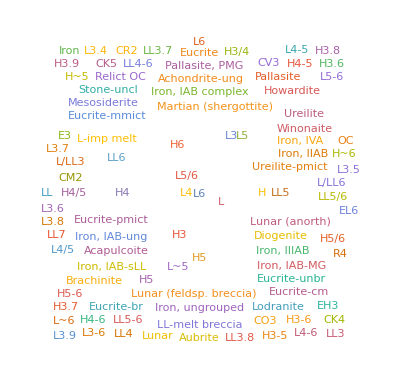

```mathematica
meteoriteData[WordCloud,"Classification"]
```

### The Wolfram Knowledgebase

The Wolfram Language™ makes it easier to create standardized computable description of real-world constructs and data. Free-form linguistics can be used to access the continuously updated Wolfram Knowledgebase™ (also used in Wolfram|Alpha®).

Type in Ctrl+= to provide a natural language input:

-Graphics-

```mathematica
Entity["Country","UnitedStates"]
```

United States

Look at the InputForm of "United States":

```mathematica
Entity["Country","UnitedStates"]//InputForm
```

Entity["Country", "UnitedStates"]

An Entity is a canonical object representing some real-world data.

The available properties of an Entity can be viewed with:

```mathematica
Entity["Country","UnitedStates"]["Properties"]
```

{adjusted net national income,seasonal bank borrowings from Fed, plus adjustments,regions,adult population,obese adults,number of aggravated assaults,rate of aggravated assault,aggregate home value,aggregate home value, householder 15 to 24 years,aggregate home value, householder 25 to 34 years,aggregate home value, householder 35 to 64 years,aggregate home value, householder 65 years and over,aggregate household income,aggregate weekly hours index,agricultural irrigated land fraction,agricultural land fraction,agricultural production index,agricultural production per capita index,agricultural products,consumption,consumption per capita,harvest area,harvest area per capita,production,production per capita,average yield,yield per capita,arrivals by air,aircraft carriers,air force,airports,air transport,alcohol fuel,total primary energy,alternate names,AM radio stations,annual annulments,annual births,annual deaths,annual divorces,annual HIV/AIDS deaths,annual marriages,antenatal care coverage,annual-crop land area,annual-crop land fraction,total area,armored infantry fighting vehicles,armored personnel carriers,army,artillery,attack helicopters,automobile production,average hourly earnings,average length of stay,average number of meetings with tax officials,average time to clear exports through customs,average weekly hours,average weekly overtime hours,aviation gasoline,bankers acceptance rate,bank prime loan rate,bank prime loan rate changes,benefits cost index,birth rate fraction,births attended by skilled health personnel,births by caesarean section,book titles published,bordering countries/regions,shared border lengths,full boundary length,burden of customs procedure,number of burglaries,rate of burglary,business activity index,professional arrivals,business entry rate,business extent of disclosure,calling code,capacity utilization rate,capital city,capital location,S&P/Case-Shiller home price index,central bank intervention,certificate of deposit,changes in inventories,checkable deposits,chemicals fraction of manufacturing value added,child employment,child population,vitamin A supplementation,children not enrolled in schools,overweight children,antimalarial treatment for fever,stunted children,underweight children,children with ARI symptoms taken to facility,diarrheal treatment with ORT,children sleeping under insecticide-treated nets,cinema attendance,number of cinemas,cinema seats,civilian employment population ratio,civilian labor force,civilian participation rate,civilian unemployment rate,classes,climate types,lignite brown coal,coal,coal,coast guard,coastline length,commercial banks assets,commercial banks credit,commercial paper,commercial paper of nonfinancial companies,community and traditional health workers,community and traditional health workers per capita,compensation per hour index,school completion rate,prevalence of condom use by young people,construction value added,consumer credit,consumer price index,consumer sentiment,container port traffic,continent,contraceptive prevalence,contributing family workers,contributing family workers fraction,conventional mortgage rate,corporate bond yield,corporate capital consumption adjustment,corporate cash flow,corporate dividends,corporate inventory valuation adjustment,corporate profits,corporate proprietors income,typical cost of business start up procedures,typical cost to export one container,typical cost to import one container,country code,consumer price index,CPIA rating,credit depth of information,total rate of crime,total number of crimes,perennial-crop land area,perennial-crop land fraction,currency code,currency in circulation,currency name,currency short name,currency unit,current account,current account balance,current expenditure on health,average daily hotel stays,daily newspaper circulation,death rate fraction,debt measure,DEC alternative conversion factor,demand deposits,dentistry personnel,dentistry personnel per capita,dependencies,dependency parent,deposit interest rate,deposits with Federal Reserve banks,destroyers,discount rate changes,discount window borrowing,discrepancy in expenditure estimate of GDP,disposable personal income,typical documents required per export shipment,typical documents required per import shipment,improved drinking water sources,natural gas,natural gas,ease of doing business,economic aid,economically active children,total school duration,effective federal funds rate,elderly population,electrical grid frequency,electrical grid plug images,electrical grid plug codes,electrical grid socket images,electrical grid socket codes,electrical grid voltages,electricity from biomass,electricity from fossil fuels,geothermal electricity,hydroelectric electricity,pumped-storage hydroelectricity,nuclear electricity,electricity from solar, tide, or waves,total electricity,electricity from renewables,electricity from wind,falling water resources for electric power,emigration rate of tertiary educated,employees compensation,self-employed with employees,employers fraction,employment,employment cost index,employment fraction,employment to population ratio,school ending age,entity classes,environmental agreements,environmental issues,ethnic groups,ethnic mix,exchange rate,expenditure fractions,expenditure on ancillary services,expenditure on day care,health spending,expenditure on home health care,expenditure on in-patient care,expenditure on medical services,expenditure on out-patient care,expenditure on over-the-counter medicines,expenditure on prescription medicines,expenditure per student,expenditure per student fraction of GDP per capita,export commodities,export partners,export partners fractions,exports as a capacity to import,export value,extended credit borrowings,external balance,external debt,factors affecting reserve balances of depository institutions,federal debt,federal deficit,federal demand deposits,federal demand deposits and note balances,federal investment,federal note balances,Federal Reserve bank discount rate,federal surplus,female adult population,female child population,female elderly population,female infant mortality fraction,female life expectancy,female median age,female population,fertilizer consumption,fertilizer production,FHA mortgage rate,fighters,ground-attack fighters,final consumption expenditure,final sales of domestic product,final sales to domestic purchasers,firms formally registered when operations started,firms offering formal training,firms using banks to finance investment,firms with female participation in ownership,fiscal year date,fish production,fixed broadband internet subscribers,fixed capital consumption,flag,flag description,flag image,flexible seasonal credit rate,FM radio stations,food, beverages and tobacco fraction of manufacturing value added,food production index,food production per capita index,number of rapes,rate of rape,foreign exchange reserves,change in foreign owned assets,foreign owned ships,foreign registered ships,forest and woodland area,freshwater withdrawals,freshwater withdrawals fraction,frigates,full coordinates,full name,full native names,gas-diesel oils,GDP,GDP deflator,GDP per employed person,general government final consumption expenditure,Gini index,gross national income,government consumption expenditures and gross investment,government current expenditures,government current receipts,government debt,government education spending as portion of GNI,government investment,government receipts,government saving,government surplus,grants in aid,greenhouse gas emissions,gross capital formation,gross domestic income,GDP,Gross Domestic Purchases,gross domestic savings,gross fixed capital formation,gross national expenditure,gross national expenditure deflator,GNP,gross savings,GSP,gross value added at factor cost,groups,total guests in hotels and similar accommodations,has polygon?,Human Development Index,highest elevation,highest point,HIV-AIDS death rate fraction,HIV/AIDS fraction,HIV/AIDS population,home ownership rate,hospital beds,hours worked index,household credit market outstanding debt,household debt service,household final consumption expenditure,household financial obligation,FHFA home price index,FHFA home price index annual average,new single-family home sales,housing affordability index,housing permits,housing starts,households,illiteracy rate,implicit price deflator,import commodities,import partners,import partners fractions,import value,improved sanitation,income payments,income receipts,income share,independence date,independence year,industrial production,industrial production growth,infant mortality fraction,infectious diseases,inflation rate,inflation expectation,inflation rate,informal payments to public officials,institutional money funds,intake rate in grade 1,interest rate spread,international migrant stock,international organizations,international organizations observer,internet code,internet hosts,average broadband download rate,average broadband upload rate,internet usage,inventory to sales ratio,investment on medical facilities,IP addresses,total IRA and Keogh accounts,irrigated land area,irrigated land fraction,Islamic Revolutionary Guard corps,firms with ISO quality certification,ISO name,International Telecommunication Union region,laboratory health workers,laboratory health workers per capita,labor force,labor force fraction,labor participation rate,land area,crop land area,languages,language dialects,language fractions,number of larcenies,rate of larceny,largest cities,latitude,lead time to export,lead time to import,annual abortions,leisure arrivals,lending interest rate,license plate code,life expectancy,liner shipping connectivity index,liquid assets,literacy rate,livestock population,logistics performance index,longitude,long-term unemployment rate,losses due to theft, robbery, vandalism, and arson,lowest elevation,lowest point,M2 interest rate,M2 minus interest rate,machinery and transport equipment fraction of manufacturing value added,main battle tanks,major industries,major ports,male adult population,male child population,male elderly population,male infant mortality fraction,male life expectancy,male median age,male population,management time dealing with officials,manufacturers new orders,marine corps,protected fraction of territorial waters,maritime claims,meat production,median age,median home sale price,median home value,median household income,memberships,merchant ships,merchant ships dead weight,merchant ships gross,merchant ship types,military age females,military age males,military age population,military age rate,military expenditure fraction,military expenditures,military fit females,military fit males,military fit population,minimum wage,miscellaneous value added,mobile cellular subscriptions,monetary base,monetary services index,money multiplier,money supply,motor gasoline,number of motor vehicle thefts,rate of motor vehicle thefts,multifactor productivity,incidents of murder and nonnegligent manslaughter,rate of murder and nonnegligent manslaughter,MZM interest rate,name,national gendarmerie,national guard,national income,nationality name,native names,natural gas exports,natural gas imports,natural gas reserves,natural gas price,natural hazards,natural resources,natural resources rents,navy,neonates protected against neonatal tetanus,net current transfers from abroad,net income from abroad,net migration,newborns with low birth weight,new businesses registered,newspaper circulation,number of newspaper titles,size of nuclear stockpile,number of owner-occupied housing units,number of marine protected areas,teachers,number of terrestrial protected areas,nursing and midwifery personnel,nursing and midwifery personnel per capita,official languages,oil exports,oil imports,oil reserves,DTP immunization,hepatitis B immunization,Hib immunization,MCV immunization,other arrivals,other checkable deposits,other health service providers,other manufacturing fraction of manufacturing value added,economic output,output per hour,total hotel nights,overnight term Eurodollars,overnight and term RPs,paper and paperboard production,part time employment,part time employment fraction,paved airport lengths,paved airports,paved roads fraction,per capita income,persistence to grade 5,persistence to last grade of primary,personal consumption expenditures,personal income,personal saving,personal saving rate,crude oil,crude oil,natural gas plant liquids,natural gas plant liquids,total petroleum,petroleum,pharmaceutical personnel,pharmaceutical personnel per capita,physicians,physicians per capita,pipelines,PMI composite index,polygon,population,population by educational attainment,population by migration in previous 12 months,population by language spoken at home,population by marital status,population by poverty status,population by school enrollment,population density,population growth,center coordinates,potential GDP,poverty gap,poverty fraction,PPP conversion factor gdp,PPP conversion factor for private consumption,presidential guard,price index,primary credit,private credit bureau coverage,private domestic investment,private fixed investment,private inventories change,private saving,producer price index,progression to secondary school,total rate of property crime,total number of property crimes,proportion of seats held by women in national parliaments,public credit registry coverage,public spending on education,public education spending,pump price for diesel fuel,pump price for gasoline,students,fraction of students,student/teacher ratio,quality of port infrastructure,radio receivers,radio stations,arrivals by rail,railway length,railway gauge lengths,railway gauge rules,rail transport,ratio of female to male students,ratio of young literate female to male,real effective exchange rate index,real interest rate,refinery gain/loss,refinery production,refugees from other countries,refugees in other countries,region names,religions,renewable internal freshwater resources,rental income of persons,students repeating a grade,required reserves,research and development researchers,reserve adjustment magnitude,reserve air force,reserve army,reserve balances,reserve bank credit,reserve marine corps,reserve navy,reserves,retail money funds,retail sales,risk premium on lending,road accidents causing injury,road accidents causing injury per amount of traffic,road accidents causing injury per population,people injured in road accidents,people injured in road accidents per amount of traffic,people injured in road accidents per population,people killed in road accidents,people killed in road accidents per amount of traffic,people killed in road accidents per population,arrivals by road,highways density,length of highways,motorways density,length of motorways,other roads density,length of other road types,total road density,secondary roads density,length of secondary roads,total road length,road transport,road sector diesel fuel consumption,road sector energy consumption,road sector energy consumption fraction,road sector gasoline fuel consumption,bus traffic,motorcycle traffic,passenger car traffic,total road traffic,truck and van traffic,number of robberies,rate of robbery,roundwood production,saving,savings deposits,savings and small time deposits,sawnwood production,schematic polygon,school enrollment fraction,seasonal bank borrowings from Fed,sector labor fractions,secure internet servers,securities lent to dealers,self employed,self employed fraction,service related deposits,shape,share of women employed,short wave radio stations,signed environmental agreements,spot oil price,school starting age,start up procedures to register a business,statistical discrepancy,strength of legal rights,submarines,suffrage type,target federal funds rate,number of business taxes,telephone lines,television receivers,television stations,terms of trade adjustment,terrain types,terrestrial protected areas,textiles and clothing fraction of manufacturing value added,time deposits,typical time required to build a warehouse,typical time required to enforce a contract,typical time required to obtain an operating license,typical time required to register property,typical time required to start a business,total time and savings deposits,time to prepare and pay taxes,time to resolve insolvency,time zones,current tobacco use among adolescents,current tobacco use among adults,total annual visitors,total borrowings,total registered businesses,total business inventory,total business tax rate,total fertility rate,trade value,trade balance,trade deficit,trade value added,trade-weighted exchange index,transportation value added,traveler's checks outstanding,treasury security,treasury average yield,treasury deposits,treasury securities composite rate,UN code,unemployed people,unemployment average duration,unemployment median duration,unemployment rate,unilateral current transfers,unit labor cost,unit nonlabor cost,UN number,unpaved airport lengths,unpaved airports,unpaved road length,unweighted sample housing units,unweighted sample population,uranium,change in US owned assets abroad,GDP value added,losses due to electrical outages,vault cash,vehicle sales,buses in use,buses in use per road length,buses in use per population,motorcycles in use,motorcycles in use per road length,motorcycles in use per population,passenger cars in use,passenger cars in use per road length,passenger cars in use per population,total vehicles in use,total vehicles in use per road length,total vehicles in use per population,trucks and vans in use,trucks and vans in use per road length,trucks and vans in use per population,total rate of violent crime,total number of violent crimes,vulnerable employment,vulnerable employment fraction,wage and salaried workers,wage and salaried workers fraction,wage cost index,water area,arrivals by sea,water productivity,waterway length,employment,wholesale price index}

The value of a specific property is obtained by:

```mathematica
Entity["Country","UnitedStates"]["Area"]
```

3.71871×10^6 mi^2

Currently available Entity Types can be listed with:

```mathematica
EntityValue[]
```

{AdministrativeDivision,Aircraft,Airline,Airport,Alphabet,AmusementPark,AmusementParkRide,AmusementParkType,AnatomicalConceptIdentifier,AnatomicalFunctionalConcept,AnatomicalSpatialConcept,AnatomicalStructure,AnatomicalTemporalConcept,AnimalAnatomicalStructure,AnimalCoatColorAndPattern,AnimalEggColor,AnimalFeatherColor,AnimalSkinColor,AnimalUse,Artwork,AstronomicalObservatory,AstronomicalRadioSource,AtmosphericLayer,BasicFoodGroup,Beach,BoardGame,Book,Bridge,BridgeType,BroadcastStation,BroadcastStationClassification,Building,Canal,Castle,CatBreed,CattleBreed,Cave,Cemetery,Character,Chemical,City,ClimateType,Cloud,CognitiveTask,Color,ColorSet,Comet,Company,ComputationalComplexityClass,Concept,Constellation,ContinuedFraction,ContinuedFractionResult,ContinuedFractionSource,Country,CrystalFamily,CrystallographicSpaceGroup,CrystalSystem,CurrencyDenomination,customers,Dam,DeepSpaceProbe,Desert,Digimon,Dinosaur,Disease,DisplayFormat,DistrictCourt,DogBreed,EarthImpact,Earthquake,EclipseType,Element,Emotion,employees,EthnicGroup,Exoplanet,FamousChemistryProblem,FamousGem,FamousMathGame,FamousMathProblem,FamousPhysicsProblem,FAOConservationStatus,FictionalCharacter,FictionalPlace,FictionalSpecies,FileFormat,Financial,FiniteGroup,Food,FoodAge,FoodAlcoholLabel,FoodBeefGrade,FoodBoneContent,FoodBrandName,FoodCaffeineLabel,FoodCalorieLabel,FoodComposition,FoodConcentration,FoodCrustType,FoodCulture,FoodDataSource,FoodFatLabel,FoodFatType,FoodFiberLabel,FoodFlavor,FoodGeometryType,FoodIntendedUse,FoodIronLabel,FoodLocation,FoodManufacturer,FoodMeatCut,FoodMeatQuality,FoodMoistureLevel,FoodNutritionalSupplement,FoodNutritionalSupplementNotAdded,FoodPackaging,FoodPart,FoodPattyCount,FoodPeelingType,FoodPreparation,FoodProcessingType,FoodSeafoodVariety,FoodSeedContent,FoodServingType,FoodShape,FoodSize,FoodSkinContent,FoodSodiumLabel,FoodState,FoodStorageType,FoodSubBrandName,FoodSugarLabel,FoodSugarType,FoodTexture,FoodTrimmingLevel,FoodType,FoodTypeGroup,FoodVariety,FoodVegetablePart,Forest,FrequencyAllocation,FunctionalAnalysisSource,FunctionSpace,Galaxy,Gender,Gene,GeographicRegion,GeologicalLayer,GeologicalPeriod,GeometricScene,GivenName,Glacier,GoatBreed,GrammaticalUnit,Graph,HistoricalCountry,HistoricalEvent,HistoricalPeriod,HistoricalSite,HorseBreed,HorseBreedConservationStatus,HorseCoatColorAndPattern,HorseType,HorseUse,ICDNine,ICDTen,Icon,IntegerSequence,InternetDomain,IPAddress,Island,ISO15924Group,Isotope,Knot,Lake,Lamina,Language,Laser,Lattice,LatticeSystem,LibraryBranch,LibrarySystem,LightColor,MannedSpaceMission,MathematicalFunction,MathWorld,MatterPhase,MeasurementDevice,MedicalTest,MeteorShower,MetropolitanArea,MilitaryConflict,MilitaryConflictType,Mine,Mineral,MinorPlanet,MoonPhase,Mountain,Movie,MPAARating,Museum,MusicAct,MusicAlbum,MusicAlbumRelease,MusicalInstrument,MusicWork,MusicWorkRecording,Mythology,NaturalHazard,NaturalResource,Nebula,Neighborhood,NetworkService,Neuron,NonperiodicTiling,NotableComputer,NuclearExplosion,NuclearReactor,NuclearTestSite,ObjectStatus,Ocean,offices,OilField,OperatingStatus,orderdetails,orders,Park,Particle,ParticleAccelerator,payments,Periodical,PeriodicTiling,Person,PersonTitle,PhysicalActivity,PhysicalConstant,PhysicalSystem,PigBreed,PigeonBreed,PilatesExercise,PlaneCurve,Planet,PlanetaryMoon,Plant,Pokemon,PokemonAbilities,PokemonGeneration,PokemonPokedexColor,PokemonType,Polyhedron,PopularCurve,PoultryBreed,PoultryBreedConservationStatus,PreservationStatus,PrivateSchool,productlines,products,ProgrammingLanguage,Protein,PublicSchool,Pulsar,Reef,Religion,ReserveLand,RiemannHypothesisFormulation,River,Rocket,RocketFunction,Satellite,SchoolDistrict,SheepBreed,Ship,Shipwreck,SNP,SolarSystemFeature,Solid,Sound,Source,SpaceCurve,Species,SportMatch,SportObject,Stadium,Star,StarCluster,StatisticalGroup,StormType,Supernova,SupernovaType,Surface,Surname,SystemModel,TerrainType,TidalConstituent,TideStation,TimeZone,TopLevelDomain,TopologicalSpaceType,Transparency,TropicalStorm,Tunnel,UnderseaFeature,University,USCongressionalDistrict,USDAEggSize,USDAFoodGroup,VisualArtsArtForm,VisualArtsArtGenre,Volcano,Waterfall,WeatherStation,WolframDemonstration,WolframLanguageSymbol,Word,WritingDirection,WritingScript,WritingScriptBaseline,WritingScriptLigature,WritingScriptStatus,WritingScriptType,WritingScriptWhiteSpace,YogaPose,YogaPosition,YogaProp,YogaSequence,ZIPCode}

A list of sample entities can be obtained by:

```mathematica
EntityValue[Entity["Country"],"SampleEntities"]
```

{United States,Chile,China,France,Nigeria,Norway,Japan,Indonesia,Liechtenstein,New Zealand}

An EntityClass represents a class of entities of a specific type. The type can be an implicitly defined entity or a representation of a table (or virtual table) in a database.

A class of entities representing all the countries in North America:

```mathematica
EntityClass["Country","NorthAmerica"]
```

North America

```mathematica
EntityList[%]
```

{Anguilla,Antigua and Barbuda,Aruba,Bahamas,Barbados,Belize,Bermuda,British Virgin Islands,Canada,Cayman Islands,Costa Rica,Cuba,Curacao,Dominica,Dominican Republic,El Salvador,Greenland,Grenada,Guadeloupe,Guatemala,Haiti,Honduras,Jamaica,Martinique,Mexico,Montserrat,Nicaragua,Panama,Puerto Rico,Saint Kitts and Nevis,Saint Lucia,Saint Pierre and Miquelon,Saint Vincent and the Grenadines,Sint Maarten,Trinidad and Tobago,Turks and Caicos Islands,United States,United States Virgin Islands}

The guide on Knowledge Representation & Access provides more information on the Wolfram Language representations of entities and their properties.

The Wolfram Language also supports custom entity stores that allow the same computations as the built-in knowledgebase and can be associated with external relational databases.

The Wolfram Language also provides a more traditional collection of high-quality curated datasets spanning a variety of topics:

Physics and Chemistry Data

Earth Sciences Data

Engineering Data, Transportation Data

Socioeconomic & Demographic Data

Life Sciences & Medicine Data

ExampleData

List the names of types of examples:

```mathematica
ExampleData[]
```

{AerialImage,Audio,ColorTexture,Dataset,Geometry3D,LinearProgramming,MachineLearning,Matrix,NetworkGraph,Sound,Statistics,TestAnimation,TestImage,TestImage3D,TestImageSet,Text,Texture}

List of the elements or properties available for a particular example:

```mathematica
ExampleData[{"Text","USConstitution"},"Properties"]
```

{Author,FormattedText,FullTitle,Language,Lines,NotebookExpression,String,Title,Words}

## Getting Data from Files

Data in various formats can be imported from existing data files found either on your local system or on the web.

Formats associated with typical data files:

Text and numeric data: .txt, .csv, .tsv, .xls, .xlsx

Images: .bmp, .jpeg, .png, .tiff, .svg

Structured web data: .html, .json, .xml

Archives: .zip, .gzip, .tar

Domain specific:

Chemical and biomolecular formats: MOL, Affymetrix, AgilentMicroarray, FASTA, GenBank, ...

Geospatial formats: ArcGRID, GeoTIFF, GeoJSON, GPX, ...

Many others

Formats supported in the Wolfram Language: (Has 226 different file types as acceptable)

```mathematica
$ImportFormats //Length
```

226

When working with data files, it is helpful to set a working directory:

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"data"}]]
```

C:\Users\vlada\OneDrive\Documents\Wolfram Data Science Boot Camp\Day 5\MPDSWorkflow\data

List the names of the files in a selected directory using FileNames:

```mathematica
FileNames[]
```

{cities.xlsx,creatures.mx,.DS_Store,gauges.mx,stockdata.csv}

```mathematica
FileNames["*.csv"]
```

{stockdata.csv}

Import data files from the local “data” directory (type in the file name (with complete path) or from the menu select Insert ▶ File Path…):

```mathematica
stockdata =Import["stockdata.csv"];
```

```mathematica
citydata = Import["cities.xlsx"];
```

Take a peek at the data:

```mathematica
Shallow[stockdata]
```

{{Jul 03 2006,11228.},{Jul 05 2006,11151.8},{Jul 06 2006,11225.3},{Jul 07 2006,11090.7},{Jul 10 2006,11103.6},{Jul 11 2006,11134.8},{Jul 12 2006,11013.2},{Jul 13 2006,10846.3},{Jul 14 2006,10739.4},{Jul 17 2006,10747.4},«53»}

```mathematica
First[citydata]
```

{{City,Country,Population},{Tokyo,Japan,8.3×10^6},{Chicago,United States,2.8×10^6},{London,United Kingdom,7.4×10^6},{Berlin,Germany,3.4×10^6}}

Import files directly from the web using the URL:

```mathematica
meteoriteDataRaw =Import["https://data.nasa.gov/api/views/gh4g-9sfh/rows.csv"];
```

```mathematica
meteoriteDataRaw//First
```

{name,id,nametype,recclass,mass (g),fall,year,reclat,reclong,GeoLocation}

What elements are available for import:

```mathematica
Import["stockdata.csv","Elements"]
```

{Data,Dataset,Dimensions,Grid,MaxColumnCount,RawData,RowCount,Summary}

```mathematica
Import["https://data.nasa.gov/api/views/gh4g-9sfh/rows.csv","Elements"]
```

{Data,Dataset,Dimensions,Grid,MaxColumnCount,RawData,RowCount,Summary}

A summary of information about the file itself:

```mathematica
Import["stockdata.csv","Summary"]
```

A useful approach to save mid-workflow restructured data is to save Wolfram Language expressions and definitions using Save and DumpSave and read it in using Get.

Create some temporary results:

```mathematica
tmpResults = GroupBy[Rest[meteoriteDataRaw],Part[#,4]&]
```

<|L5→{{Aachen,1,Valid,L5,21,Fell,01/01/1880 12:00:00 AM,50.775,6.08333,(50.775, 6.08333)},{Northwest Africa 5815,50693,Valid,L5,256.8,Found,,0.,0.,(0.0, 0.0)},4814,{Zelfana,31353,Valid,L5,1058,Found,01/01/2002 12:00:00 AM,32.1583,4.63333,(32.15833, 4.63333)}},453,L/LL→{{Yamato 86745,8,(-71.5, 35.66667)}}|>
 |  |  |  |

Save as “plain text”:

```mathematica
Save["tempData",tmpResults]
```

For large or complicated definitions, it is more efficient to store in internal Wolfram System™ format:

```mathematica
DumpSave["tmp.mx",tmpResults]
```

{<|L5→{{Aachen,1,Valid,L5,21,Fell,01/01/1880 12:00:00 AM,50.775,6.08333,(50.775, 6.08333)},{Northwest Africa 5815,50693,Valid,L5,256.8,Found,,0.,0.,(0.0, 0.0)},4814,{Zelfana,31353,Valid,L5,1058,Found,01/01/2002 12:00:00 AM,32.1583,4.63333,(32.15833, 4.63333)}},453,L/LL→{{Yamato 86745,8,(-71.5, 35.66667)}}|>}
 |  |  |  |

```mathematica
FindFile["tmp.mx"]
```

C:\Users\vlada\OneDrive\Documents\Wolfram Data Science Boot Camp\Day 5\MPDSWorkflow\data\tmp.mx

```mathematica
Clear[tmpResults]
```

```mathematica
<<"tmp.mx"
```

## Scraping Data off Webpages

Import the entire webpage as a String:

```mathematica
wolframWebpage =Import["https://www.wolfram.com/language"]
```

WolframAlpha.com WolframCloud.com All Sites & Public Resources...    
 
                
  Products & Services  
 
Wolfram|One Mathematica Wolfram|Alpha Notebook Edition Programming Lab Finance Platform SystemModeler Wolfram Player Wolfram Engine WolframScript  
 
Enterprise Private Cloud Enterprise Mathematica Wolfram|Alpha Appliance   Enterprise Solutions  
Corporate Consulting Technical Services Wolfram|Alpha Business Solutions    
Resource System  
Data Repository Neural Net Repository Function Repository   Wolfram|Alpha  
Wolfram|Alpha Pro Problem Generator API   Data Drop  
Products for Education Mobile Apps  
Wolfram Player Wolfram Cloud App Wolfram|Alpha for Mobile Wolfram|Alpha-Powered Apps   Services  
Paid Project Support Wolfram U Summer Programs       All Products & Services »       Technologies  
 
    Wolfram Language   Revolutionary knowledge-based programming language.       Wolfram Cloud   Central infrastructure for Wolfram's cloud products & services.       Wolfram Science   Technology-enabling science of the computational universe.      
    Wolfram Notebooks   The preeminent environment for any technical workflows.       Wolfram Engine   Software engine implementing the Wolfram Language.       Wolfram Natural Language Understanding System   Knowledge-based broadly deployed natural language.      
    Wolfram Data Framework   Semantic framework for real-world data.       Wolfram Universal Deployment System   Instant deployment across cloud, desktop, mobile, and more.       Wolfram Knowledgebase   Curated computable knowledge powering Wolfram|Alpha.         All Technologies »       Solutions  
 
Engineering, R&D  
Aerospace & Defense Chemical Engineering Control Systems Electrical Engineering Image Processing Industrial Engineering Mechanical Engineering Operations Research More...    
Finance, Statistics & Business Analysis  
Actuarial Sciences Bioinformatics Data Science Econometrics Financial Risk Management Statistics More...    
Education  
All Solutions for Education   Trends  
Machine Learning Multiparadigm Data Science Internet of Things High-Performance Computing Hackathons    
Software & Web  
Software Development Authoring & Publishing Interface Development Web Development   Sciences  
Astronomy Biology Chemistry More...       All Solutions »       Learning & Support  
 
Learning  
Wolfram Language Documentation Fast Introduction for Programmers Wolfram U Videos & Screencasts   
Wolfram Language Introductory Book Webinars & Training Summer Programs Books    
Need Help?  
Support FAQ Wolfram Community Contact Support    
Premium Support  
Premier Service Technical Services       All Learning & Support »       Company  
 
About  
Company Background Wolfram Blog Events Contact Us    
Work with Us  
Careers at Wolfram Internships Other Wolfram Language Jobs    
Initiatives  
Wolfram Foundation MathWorld Computer-Based Math A New Kind of Science Wolfram Technology for Hackathons Student Ambassador Program   
Wolfram for Startups Demonstrations Project Wolfram Innovator Awards Wolfram + Raspberry Pi Summer Programs More...       All Company »       Search  
   
               
 
 
    Wolfram Language ™    
Home   Principles   Uses   What's New   Resources  
For Experts   Q&A   Products & Ecosystem   Fast Introduction     Documentation   Community       Back to Latest Features           Programming with Built-in Computational Intelligence  
The Wolfram Language allows programmers to operate at a significantly higher level than ever before, by leveraging built-in computational intelligence that relies on a vast depth of algorithms and real-world knowledge carefully integrated over three decades. Scalable for programs from tiny to huge, with immediate deployment locally and in the cloud, the Wolfram Language builds on clear principles—and an elegant unified symbolic structure—to create what is emerging as the world's most productive programming language and the first true computational communication language for humans and AIs.      
 
     What's New        
 
     Version 12.1 Announcement        
 
     Essays on the Wolfram Language by Stephen Wolfram        
 
     Watch Livestreams of the Wolfram Language Being Designed            
       Principles and Concepts        Fast Introduction for Programmers        Scope and Documentation    
       For Language Experts        Products and Ecosystem        Where to Use the Wolfram Language        
  Tools and Resources for Software Developers »  
 
       Download the Free Wolfram Engine for Developers          Things to Try
Notebook    
     Start Writing Your
Own Code in the Cloud          
  New to Programming?  
 
       Stephen Wolfram's Online Book: An Elementary Introduction to the Wolfram Language          Explore with Wolfram
Programming Lab FREE               More Resources  
 
Q&A Blog Wolfram Community    
Code Gallery Tweet-a-Program Code Cards  
Programming Challenges For Hackathons Livecoding  
Open Courses & Training Interactive Demonstrations Download Brochure        
 
 
 
 
Products Wolfram|One Mathematica Wolfram|Alpha Notebook Edition Programming Lab Wolfram|Alpha Pro Mobile Apps Finance Platform SystemModeler Wolfram Player Wolfram Engine WolframScript Wolfram Workbench Volume & Site Licensing Enterprise Private Cloud View all...    
 
Services Technical Services Corporate Consulting  
For Customers Online Store Product Registration Product Downloads Service Plans Benefits User Portal Your Account  
Support Support FAQ Customer Service Contact Support    
 
Learning Wolfram Language Documentation Wolfram Language Introductory Book Fast Introduction for Programmers Fast Introduction for Math Students Webinars & Training Wolfram U Summer Programs Videos Books    
 
Public Resources Wolfram|Alpha Demonstrations Project Resource System Connected Devices Project Wolfram Data Drop Wolfram + Raspberry Pi Wolfram Science Computer-Based Math MathWorld Hackathons Computational Thinking View all...    
 
Company Events About Wolfram Careers Contact  
Connect Wolfram Community Wolfram Blog Newsletter      
 
  © 2020 Wolfram . All rights reserved.    
 
Legal & Privacy Policy Site Map WolframAlpha.com WolframCloud.com          

Enable JavaScript to interact with content and submit forms on Wolfram websites. Learn how »

Check the types of elements that can be imported from the webpage:

```mathematica
wolframWebpageHTML =Import["https://www.wolfram.com/language","Elements"]
```

{Data,FullData,Hyperlinks,ImageLinks,Images,Plaintext,Source,Title,XMLObject}

Import only the images from the webpage:

```mathematica
wolframImages =Import["https://www.wolfram.com/language","Images"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Import only the hyperlinks on the webpage:

```mathematica
wolframLinkOuts =Import["https://reference.wolfram.com/language","Hyperlinks"]
```

{http://www.wolframalpha.com/?source=nav,https://www.wolframcloud.com/?source=nav,http://www.wolfram.com/resources/?source=nav,http://www.wolfram.com/?source=nav,http://www.wolfram.com/products/?source=nav,http://www.wolfram.com/wolfram-one/?source=nav,http://www.wolfram.com/mathematica/?source=nav,http://www.wolfram.com/wolfram-alpha-notebook-edition/?source=nav,http://www.wolfram.com/programming-lab/?source=nav,http://www.wolfram.com/finance-platform/?source=nav,http://www.wolfram.com/system-modeler/?source=nav,http://www.wolfram.com/player/?source=nav,http://www.wolfram.com/engine/?source=nav,http://www.wolfram.com/wolframscript/?source=nav,http://www.wolfram.com/enterprise-private-cloud/?source=nav,http://www.wolfram.com/mathematica-enterprise-edition/?source=nav,http://products.wolframalpha.com/appliance/?source=nav,http://www.wolframsolutions.com/?source=nav,http://www.wolfram.com/support/technical-services/?source=nav,http://products.wolframalpha.com/business/?source=nav,https://datadrop.wolframcloud.com/?source=nav,https://resources.wolframcloud.com/?source=nav,https://datarepository.wolframcloud.com/?source=nav,https://resources.wolframcloud.com/NeuralNetRepository/?source=nav,https://resources.wolframcloud.com/FunctionRepository/?source=nav,http://www.wolframalpha.com/?source=nav,http://www.wolframalpha.com/pro/?source=nav,http://www.wolframalpha.com/pro/problem-generator/?source=nav,http://products.wolframalpha.com/api/?source=nav,https://datadrop.wolframcloud.com/?source=nav,http://www.wolfram.com/education/?source=nav,http://www.wolfram.com/player-app/?source=nav,http://www.wolfram.com/cloud-app/?source=nav,http://products.wolframalpha.com/mobile/?source=nav,http://products.wolframalpha.com/mobile/?source=nav#wapowered,http://www.wolfram.com/support/technical-services/?source=nav,http://www.wolfram.com/wolfram-u/?source=nav,http://education.wolfram.com/summer/?source=nav,http://www.wolfram.com/education/?source=nav,http://www.wolfram.com/player-app/?source=nav,http://www.wolfram.com/cloud-app/?source=nav,http://products.wolframalpha.com/mobile/?source=nav,http://products.wolframalpha.com/mobile/?source=nav#wapowered,http://www.wolfram.com/support/technical-services/?source=nav,http://www.wolfram.com/wolfram-u/?source=nav,http://education.wolfram.com/summer/?source=nav,http://www.wolfram.com/products/?source=nav,http://www.wolfram.com/technologies/?source=nav,http://www.wolfram.com/language/?source=nav,http://www.wolfram.com/notebooks/?source=nav,http://www.wolfram.com/data-framework/?source=nav,http://www.wolfram.com/cloud/?source=nav,http://www.wolfram.com/engine/?source=nav,http://www.wolfram.com/universal-deployment-system/?source=nav,http://www.wolfram.com/wolfram-science/?source=nav,http://www.wolfram.com/natural-language-understanding/?source=nav,http://www.wolfram.com/knowledgebase/?source=nav,http://www.wolfram.com/technologies/?source=nav,http://www.wolfram.com/solutions/?source=nav,http://www.wolfram.com/solutions/industry/aerospace-engineering/?source=nav,http://www.wolfram.com/solutions/industry/chemical-engineering/?source=nav,http://www.wolfram.com/solutions/industry/control-systems/?source=nav,http://www.wolfram.com/solutions/industry/electrical-engineering/?source=nav,http://www.wolfram.com/solutions/industry/image-processing/?source=nav,http://www.wolfram.com/solutions/industry/industrial-engineering/?source=nav,http://www.wolfram.com/solutions/industry/mechanical-engineering/?source=nav,http://www.wolfram.com/solutions/industry/operations-research/?source=nav,http://www.wolfram.com/solutions/?source=nav,http://www.wolfram.com/education/?source=nav,http://www.wolfram.com/solutions/industry/actuarial-sciences/?source=nav,http://www.wolfram.com/solutions/industry/bioinformatics/?source=nav,http://www.wolfram.com/solutions/industry/data-science/?source=nav,http://www.wolfram.com/solutions/industry/econometrics/?source=nav,http://www.wolfram.com/solutions/industry/financial-risk-management/?source=nav,http://www.wolfram.com/solutions/industry/statistics/?source=nav,http://www.wolfram.com/solutions/?source=nav,http://www.wolfram.com/developer/?source=nav,http://www.wolfram.com/solutions/industry/electronic-publishing/?source=nav,http://www.wolfram.com/solutions/industry/interface-development/?source=nav,http://www.wolfram.com/solutions/industry/web-development/?source=nav,http://www.wolfram.com/education/?source=nav,http://www.wolfram.com/featureset/machine-learning/?source=nav,http://www.mpdatascience.com/?source=nav,http://www.wolfram.com/internet-of-things/?source=nav,http://www.wolfram.com/solutions/hpc/?source=nav,http://www.wolfram.com/hackathons/?source=nav,http://www.wolfram.com/solutions/industry/astronomy/?source=nav,http://www.wolfram.com/solutions/industry/biological-sciences/?source=nav,http://www.wolfram.com/solutions/industry/chemistry/?source=nav,http://www.wolfram.com/solutions/?source=nav,http://www.wolfram.com/developer/?source=nav,http://www.wolfram.com/solutions/industry/electronic-publishing/?source=nav,http://www.wolfram.com/solutions/industry/interface-development/?source=nav,http://www.wolfram.com/solutions/industry/web-development/?source=nav,http://www.wolfram.com/solutions/industry/astronomy/?source=nav,http://www.wolfram.com/solutions/industry/biological-sciences/?source=nav,http://www.wolfram.com/solutions/industry/chemistry/?source=nav,http://www.wolfram.com/solutions/?source=nav,http://www.wolfram.com/solutions/?source=nav,http://www.wolfram.com/support/?source=nav,http://reference.wolfram.com/language/?source=nav,http://www.wolfram.com/language/fast-introduction-for-programmers/?source=nav,http://www.wolfram.com/wolfram-u/?source=nav,http://www.wolfram.com/broadcast/?source=nav,http://www.wolfram.com/language/elementary-introduction/?source=nav,http://www.wolfram.com/wolfram-u/calendar/?source=nav,http://education.wolfram.com/summer/?source=nav,http://www.wolfram.com/books/?source=nav,https://support.wolfram.com/?source=nav,http://community.wolfram.com/?source=nav,http://www.wolfram.com/support/contact/?source=nav,http://www.wolfram.com/mathematica/pricing/premier-service.php?source=nav,http://www.wolfram.com/support/technical-services/?source=nav,http://www.wolfram.com/support/?source=nav,http://www.wolfram.com/company/?source=nav,http://www.wolfram.com/company/background.html?source=nav,http://blog.wolfram.com/?source=nav,http://company.wolfram.com/events/?source=nav,http://www.wolfram.com/company/contact/?source=nav,http://www.wolfram.com/company/careers/?source=nav,http://www.wolfram.com/company/careers/?source=nav,http://community.wolfram.com/content?curTag=jobs&source=nav,http://www.wolframfoundation.org/?source=nav,http://mathworld.wolfram.com/?source=nav,http://www.computerbasedmath.org/?source=nav,http://www.wolframscience.com/?source=nav,http://www.wolfram.com/hackathons/?source=nav,http://www.wolfram.com/company/careers/ambassador/?source=nav,http://www.wolfram.com/startups/?source=nav,http://demonstrations.wolfram.com/?source=nav,http://www.wolfram.com/events/technology-conference/innovator-award/?source=nav,http://www.wolfram.com/raspberry-pi/?source=nav,http://education.wolfram.com/summer/?source=nav,http://www.wolfram.com/resources/?source=nav,http://www.wolfram.com/company/?source=nav,https://search.wolfram.com/?source=nav,http://www.wolfram.com/site-map/?source=nav,https://reference.wolfram.com/language,http://www.wolfram.com/language,https://reference.wolfram.com/language/guide/LanguageOverview.html,https://reference.wolfram.com/language/guide/ListManipulation.html,https://reference.wolfram.com/language/guide/Expressions.html,https://reference.wolfram.com/language/guide/Associations.html,https://reference.wolfram.com/language/guide/VariablesAndFunctions.html,https://reference.wolfram.com/language/guide/RulesAndPatterns.html,https://reference.wolfram.com/language/guide/FunctionalProgramming.html,https://reference.wolfram.com/language/guide/ProceduralProgramming.html,https://reference.wolfram.com/language/guide/StringManipulation.html,https://reference.wolfram.com/language/guide/ParallelComputing.html,https://reference.wolfram.com/language/guide/ExternalOperations.html,https://reference.wolfram.com/language/guide/PackageDevelopment.html,https://reference.wolfram.com/language/guide/TuningAndDebugging.html,https://reference.wolfram.com/language/guide/ComputationWithStructuredDatasets.html,https://reference.wolfram.com/language/guide/KnowledgeRepresentationAndAccess.html,https://reference.wolfram.com/language/guide/Syntax.html,https://reference.wolfram.com/language/guide/FreeFormAndExternalInput.html,https://resources.wolframcloud.com/FunctionRepository/category/core-language-structure,https://reference.wolfram.com/language/guide/ImportingAndExporting.html,https://reference.wolfram.com/language/guide/HandlingArraysOfData.html,https://reference.wolfram.com/language/guide/DataTransformsAndSmoothing.html,https://reference.wolfram.com/language/guide/Statistics.html,https://reference.wolfram.com/language/guide/MachineLearning.html,https://reference.wolfram.com/language/guide/DataVisualization.html,https://reference.wolfram.com/language/guide/AutomatedReports.html,https://reference.wolfram.com/language/guide/ComputationWithStructuredDatasets.html,https://reference.wolfram.com/language/guide/DatabaseConnectivity.html,https://reference.wolfram.com/language/guide/WDFWolframDataFramework.html,https://resources.wolframcloud.com/FunctionRepository/category/data-manipulation-analysis,https://reference.wolfram.com/language/guide/DataVisualization.html,https://reference.wolfram.com/language/guide/FunctionVisualization.html,https://reference.wolfram.com/language/guide/ChartingAndInformationVisualization.html,https://reference.wolfram.com/language/guide/GeoVisualization.html,https://reference.wolfram.com/language/guide/DynamicVisualization.html,https://reference.wolfram.com/language/guide/GraphicsOptionsAndStyling.html,https://reference.wolfram.com/language/guide/GraphicsInteractivityAndDrawing.html,https://reference.wolfram.com/language/guide/SymbolicGraphicsLanguage.html,https://reference.wolfram.com/language/guide/ImportingAndExporting.html,https://resources.wolframcloud.com/FunctionRepository/category/visualization-graphics,https://reference.wolfram.com/language/guide/MachineLearning.html,https://reference.wolfram.com/language/guide/NeuralNetworks.html,https://reference.wolfram.com/language/guide/FeatureDetection.html,https://reference.wolfram.com/language/guide/ComputerVision.html,https://reference.wolfram.com/language/guide/TextAnalysis.html,https://resources.wolframcloud.com/FunctionRepository/category/machine-learning,https://reference.wolfram.com/language/guide/MathematicalFunctions.html,https://reference.wolfram.com/language/guide/NumericalEvaluationAndPrecision.html,https://reference.wolfram.com/language/guide/MatricesAndLinearAlgebra.html,https://reference.wolfram.com/language/guide/FormulaManipulation.html,https://reference.wolfram.com/language/guide/EquationSolving.html,https://reference.wolfram.com/language/guide/Calculus.html,https://reference.wolfram.com/language/guide/Optimization.html,https://reference.wolfram.com/language/guide/ProbabilityAndStatistics.html,https://reference.wolfram.com/language/guide/DiscreteMathematics.html,https://reference.wolfram.com/language/guide/BooleanComputation.html,https://resources.wolframcloud.com/FunctionRepository/category/symbolic-numeric-computation,https://reference.wolfram.com/language/guide/PolynomialAlgebra.html,https://reference.wolfram.com/language/guide/MatricesAndLinearAlgebra.html,https://reference.wolfram.com/language/guide/Tensors.html,https://reference.wolfram.com/language/guide/Calculus.html,https://reference.wolfram.com/language/guide/DiscreteCalculus.html,https://reference.wolfram.com/language/guide/IteratedMapsAndFractals.html,https://reference.wolfram.com/language/guide/NeuralNetworks.html,https://reference.wolfram.com/language/guide/ProbabilityAndStatistics.html,https://reference.wolfram.com/language/guide/RandomProcesses.html,https://reference.wolfram.com/language/guide/DiscreteMathematics.html,https://reference.wolfram.com/language/guide/NumberTheory.html,https://reference.wolfram.com/language/guide/GroupTheory.html,https://reference.wolfram.com/language/guide/MathematicalData.html,https://reference.wolfram.com/language/guide/Cryptography.html,https://reference.wolfram.com/language/guide/LogicAndBooleanAlgebra.html,https://reference.wolfram.com/language/guide/TheoremProving.html,https://resources.wolframcloud.com/FunctionRepository/category/higher-mathematical-computation,https://reference.wolfram.com/language/guide/StringManipulation.html,https://reference.wolfram.com/language/guide/WorkingWithTemplates.html,https://reference.wolfram.com/language/guide/FreeFormAndExternalInput.html,https://reference.wolfram.com/language/guide/InterpretingStrings.html,https://reference.wolfram.com/language/guide/ImportingAndExporting.html,https://reference.wolfram.com/language/guide/ProcessingTextualData.html,https://reference.wolfram.com/language/guide/TextAnalysis.html,https://reference.wolfram.com/language/guide/LinguisticData.html,https://reference.wolfram.com/language/guide/TextSearch.html,https://reference.wolfram.com/language/guide/SequenceAlignmentAndComparison.html,https://resources.wolframcloud.com/FunctionRepository/category/strings-text,https://datarepository.wolframcloud.com/type/Text/,https://reference.wolfram.com/language/guide/GraphsAndNetworks.html,https://reference.wolfram.com/language/guide/GraphConstructionAndRepresentation.html,https://reference.wolfram.com/language/guide/GraphVisualization.html,https://reference.wolfram.com/language/guide/GraphPropertiesAndMeasurements.html,https://reference.wolfram.com/language/guide/ComputationOnGraphs.html,https://reference.wolfram.com/language/guide/SocialNetworks.html,https://resources.wolframcloud.com/FunctionRepository/category/graphs-networks,https://datarepository.wolframcloud.com/type/Graphs/,https://reference.wolfram.com/language/guide/ImageProcessing.html,https://reference.wolfram.com/language/guide/BasicImageManipulation.html,https://reference.wolfram.com/language/guide/ImageFilteringAndNeighborhoodProcessing.html,https://reference.wolfram.com/language/guide/SegmentationAnalysis.html,https://reference.wolfram.com/language/guide/ComputerVision.html,https://reference.wolfram.com/language/guide/ImageRestoration.html,https://reference.wolfram.com/language/guide/ImageGeometry.html,https://reference.wolfram.com/language/guide/MathematicalMorphology.html,https://reference.wolfram.com/language/guide/3DImages.html,https://reference.wolfram.com/language/guide/RasterImageFormats.html,https://reference.wolfram.com/language/guide/ColorProcessing.html,https://resources.wolframcloud.com/FunctionRepository/category/images,https://datarepository.wolframcloud.com/type/Image/,https://reference.wolfram.com/language/guide/GeometricComputation.html,https://reference.wolfram.com/language/guide/PlaneGeometry.html,https://reference.wolfram.com/language/guide/SolidGeometry.html,https://reference.wolfram.com/language/guide/GeometricSpecialRegions.html,https://reference.wolfram.com/language/guide/MeshRegions.html,https://reference.wolfram.com/language/guide/DerivedRegions.html,https://reference.wolfram.com/language/guide/GeometricPropertiesAndMeasures.html,https://reference.wolfram.com/language/guide/GeometricSolvers.html,https://reference.wolfram.com/language/guide/GeometricTransforms.html,https://reference.wolfram.com/language/guide/3DGeometryAndModelingFormats.html,https://reference.wolfram.com/language/guide/3DPrinting.html,https://resources.wolframcloud.com/FunctionRepository/category/geometry,https://reference.wolfram.com/language/guide/SoundAndSonification.html,https://reference.wolfram.com/language/guide/AudioProcessing.html,https://reference.wolfram.com/language/guide/SignalProcessing.html,https://reference.wolfram.com/language/guide/AudioFormats.html,https://reference.wolfram.com/language/guide/VideoProcessing.html,https://resources.wolframcloud.com/FunctionRepository/category/sound,https://reference.wolfram.com/language/guide/KnowledgeRepresentationAndAccess.html,https://reference.wolfram.com/language/guide/ListManipulation.html,https://reference.wolfram.com/language/guide/Associations.html,https://reference.wolfram.com/language/guide/ComputationWithStructuredDatasets.html,https://reference.wolfram.com/language/guide/Units.html,https://reference.wolfram.com/language/guide/DateAndTime.html,https://reference.wolfram.com/language/guide/FreeFormAndExternalInput.html,https://reference.wolfram.com/language/guide/TextAnalysis.html,https://reference.wolfram.com/language/guide/InterpretingStrings.html,https://reference.wolfram.com/language/guide/LinguisticData.html,https://reference.wolfram.com/language/guide/TextSearch.html,https://reference.wolfram.com/language/guide/WDFWolframDataFramework.html,https://reference.wolfram.com/language/guide/WolframDataRepository.html,https://reference.wolfram.com/language/guide/WolframAlphaIntegration.html,https://resources.wolframcloud.com/FunctionRepository/category/knowledge-representation-natural-language,https://datarepository.wolframcloud.com/,https://reference.wolfram.com/language/guide/DateAndTime.html,https://reference.wolfram.com/language/guide/AstronomicalComputationAndData.html,https://reference.wolfram.com/language/guide/TimeSeries.html,https://reference.wolfram.com/language/guide/SignalProcessing.html,https://resources.wolframcloud.com/FunctionRepository/category/time-related-computation,https://datarepository.wolframcloud.com/type/Time-Series/,https://reference.wolfram.com/language/guide/MapsAndCartography.html,https://reference.wolfram.com/language/guide/GeographicData.html,https://reference.wolfram.com/language/guide/LocationsPathsAndRouting.html,https://reference.wolfram.com/language/guide/Geodesy.html,https://reference.wolfram.com/language/guide/ImportingAndExporting.html,https://reference.wolfram.com/language/guide/SocioeconomicAndDemographicData.html,https://reference.wolfram.com/language/guide/WeatherData.html,https://resources.wolframcloud.com/FunctionRepository/category/geographic-data-computation,https://datarepository.wolframcloud.com/type/Geospatial-Data/,https://reference.wolfram.com/language/guide/PhysicsAndChemistryDataAndComputation.html,https://reference.wolfram.com/language/guide/AstronomicalComputationAndData.html,https://reference.wolfram.com/language/guide/EarthSciencesDataAndComputation.html,https://reference.wolfram.com/language/guide/LifeSciencesAndMedicineDataAndComputation.html,https://reference.wolfram.com/language/guide/MolecularStructureAndComputation.html,https://reference.wolfram.com/language/guide/ScientificModels.html,https://reference.wolfram.com/language/guide/ComputationalSystemsAndDiscovery.html,https://reference.wolfram.com/language/guide/ScientificDataAnalysis.html,https://reference.wolfram.com/language/guide/Units.html,https://reference.wolfram.com/language/guide/UsingConnectedDevices.html,https://resources.wolframcloud.com/FunctionRepository/category/scientific-and-medical-data-computation,https://datarepository.wolframcloud.com/,https://reference.wolfram.com/language/guide/EngineeringData.html,https://reference.wolfram.com/language/guide/SignalProcessing.html,https://reference.wolfram.com/language/guide/ImageProcessing.html,https://reference.wolfram.com/language/guide/SystemModelAnalyticsDesign.html,https://reference.wolfram.com/language/guide/ControlSystems.html,https://reference.wolfram.com/language/guide/Reliability.html,https://reference.wolfram.com/language/guide/Units.html,https://reference.wolfram.com/language/guide/UsingConnectedDevices.html,https://resources.wolframcloud.com/FunctionRepository/category/engineering-data-computation,https://reference.wolfram.com/language/guide/FinancialAndEconomicData.html,https://reference.wolfram.com/language/guide/Finance.html,https://reference.wolfram.com/language/guide/FinancialVisualization.html,https://reference.wolfram.com/language/guide/Blockchain.html,https://reference.wolfram.com/language/guide/ActuarialComputation.html,https://reference.wolfram.com/language/guide/SocioeconomicAndDemographicData.html,https://resources.wolframcloud.com/FunctionRepository/category/financial-data-computation,https://datarepository.wolframcloud.com/category/Economics/,https://reference.wolfram.com/language/guide/SocioeconomicAndDemographicData.html,https://reference.wolfram.com/language/guide/TransportationData.html,https://reference.wolfram.com/language/guide/CulturalData.html,https://reference.wolfram.com/language/guide/PeopleAndHistory.html,https://reference.wolfram.com/language/guide/LinguisticData.html,https://resources.wolframcloud.com/FunctionRepository/category/social-cultural-linguistic-data,https://datarepository.wolframcloud.com/,https://reference.wolfram.com/language/guide/NotebookBasics.html,https://reference.wolfram.com/language/guide/NotebookFormattingAndStyling.html,https://reference.wolfram.com/language/guide/LayoutAndTables.html,https://reference.wolfram.com/language/guide/PresentationsWithTheWolframSystem.html,https://reference.wolfram.com/language/guide/MathematicalTypesetting.html,https://reference.wolfram.com/language/guide/SpecialCharacters.html,https://reference.wolfram.com/language/guide/DocumentGeneration.html,https://reference.wolfram.com/language/guide/LowLevelNotebookProgramming.html,https://reference.wolfram.com/language/guide/WebFormats.html,https://reference.wolfram.com/language/guide/LocaleAndInternationalization.html,https://reference.wolfram.com/language/guide/Accessibility.html,https://resources.wolframcloud.com/FunctionRepository/category/notebook-documents-presentation,https://reference.wolfram.com/language/guide/InteractiveManipulation.html,https://reference.wolfram.com/language/guide/ViewersAndAnnotation.html,https://reference.wolfram.com/language/guide/ControlObjects.html,https://reference.wolfram.com/language/guide/CreatingFormsAndApps.html,https://reference.wolfram.com/language/guide/GeneralizedInput.html,https://reference.wolfram.com/language/guide/DynamicInteractivityLanguage.html,https://reference.wolfram.com/language/guide/CustomInterfaceConstruction.html,https://resources.wolframcloud.com/FunctionRepository/category/user-interface-construction,https://reference.wolfram.com/language/guide/WolframSystemSessions.html,https://reference.wolfram.com/language/guide/NotebookBasics.html,https://reference.wolfram.com/language/guide/StandaloneWolframLanguageKernels.html,https://reference.wolfram.com/language/guide/BackgroundAndScheduledTasks.html,https://reference.wolfram.com/language/guide/GPUComputing.html,https://reference.wolfram.com/language/guide/ParallelComputing.html,https://reference.wolfram.com/language/guide/WolframAlphaIntegration.html,https://reference.wolfram.com/language/guide/Paclets.html,https://reference.wolfram.com/language/guide/PersistentStorage.html,https://reference.wolfram.com/language/guide/WolframSystemSetup.html,https://resources.wolframcloud.com/FunctionRepository/category/system-operation-setup,https://reference.wolfram.com/language/guide/FileOperations.html,https://reference.wolfram.com/language/guide/WebOperations.html,https://reference.wolfram.com/language/guide/CallingExternalPrograms.html,https://reference.wolfram.com/language/guide/ExternalLanguageInterfaces.html,https://reference.wolfram.com/language/guide/WorkingWithTemplates.html,https://reference.wolfram.com/language/guide/UsingConnectedDevices.html,https://reference.wolfram.com/language/guide/AccessingExternalServicesAndAPIs.html,https://reference.wolfram.com/language/guide/MailMessagesEtc.html,https://reference.wolfram.com/language/guide/Channel-BasedCommunication.html,https://reference.wolfram.com/language/guide/NetworkProgramming.html,https://reference.wolfram.com/language/guide/InternetAndWebRelatedData.html,https://reference.wolfram.com/language/guide/DatabaseConnectivity.html,https://reference.wolfram.com/language/guide/ImportingAndExporting.html,https://reference.wolfram.com/language/guide/UsingTheWolframDataDrop.html,https://reference.wolfram.com/language/guide/WolframDataRepository.html,https://reference.wolfram.com/language/guide/Blockchain.html,https://reference.wolfram.com/language/guide/Cryptography.html,https://reference.wolfram.com/language/guide/WSTPAPI.html,https://resources.wolframcloud.com/FunctionRepository/category/external-interfaces-connections,https://reference.wolfram.com/language/guide/CloudFunctionsAndDeployment.html,https://reference.wolfram.com/language/guide/WebOperations.html,https://reference.wolfram.com/language/guide/CreatingAnInstantAPI.html,https://reference.wolfram.com/language/guide/CreatingFormsAndApps.html,https://reference.wolfram.com/language/guide/SharingAndEmbeddingContent.html,https://reference.wolfram.com/language/guide/WolframDataRepository.html,https://reference.wolfram.com/language/guide/BackgroundAndScheduledTasks.html,https://resources.wolframcloud.com/FunctionRepository/category/cloud-deployment,https://reference.wolfram.com/language/guide/RecentlyAddedFeatures,https://reference.wolfram.com/language/workflowguide/WorkingInNotebooks,https://reference.wolfram.com/language/workflowguide/CreatingDocumentsAndPresentations,https://reference.wolfram.com/language/workflowguide/CreatingAndOrganizingInterfaces,https://reference.wolfram.com/language/workflowguide/UsingTheWolframLanguage,https://reference.wolfram.com/language/workflowguide/WorkingWithData,https://reference.wolfram.com/language/workflowguide/WorkingWithGraphicsImagesAndSounds,https://reference.wolfram.com/language/workflowguide/WorkingInTheCloud,https://reference.wolfram.com/language/workflowguide/DeployingToWebAndMobile,https://reference.wolfram.com/language/workflowguide/RepositoriesSharingAndPublishing,https://reference.wolfram.com/language/workflowguide/InterfacingWithOtherSystems,https://reference.wolfram.com/language/workflowguide/SetupAndAdministration,https://reference.wolfram.com/language/workflowguide/SpecificApplicationAreas,https://www.wolfram.com/language/fast-introduction-for-programmers/en/,https://www.wolfram.com/language/fast-introduction-for-math-students/en/,https://www.wolfram.com/language/elementary-introduction/,https://resources.wolframcloud.com/,https://www.wolfram.com/developer/resources/,https://www.wolfram.com/products/,https://www.wolfram.com/wolfram-u/,https://reference.wolfram.com/language/guide/SummaryOfNewFeaturesIn121,https://www.wolfram.com/products#middleware,https://reference.wolfram.com/language/guide/AlphabeticalListing,https://www.wolfram.com/products/applications/,http://www.wolfram.com/wolfram-one/?source=footer,http://www.wolfram.com/mathematica/?source=footer,http://www.wolfram.com/wolfram-alpha-notebook-edition/?source=footer,http://www.wolfram.com/programming-lab/?source=footer,http://www.wolframalpha.com/pro/?source=footer,http://www.wolfram.com/products/?source=footer#mobile-apps,http://www.wolfram.com/finance-platform/?source=footer,http://www.wolfram.com/system-modeler/?source=footer,http://www.wolfram.com/player/?source=footer,http://www.wolfram.com/engine/?source=footer,http://www.wolfram.com/wolframscript/?source=footer,http://www.wolfram.com/products/workbench/?source=footer,http://www.wolfram.com/group-organization-licensing/?source=footer,http://www.wolfram.com/enterprise-private-cloud/?source=footer,http://www.wolfram.com/products/?source=footer,http://www.wolfram.com/support/technical-services/?source=footer,http://www.wolframsolutions.com/?source=footer,http://www.wolfram.com/support/technical-services/?source=footer,http://www.wolframsolutions.com/?source=footer,http://www.wolfram.com/get-products-services/?source=footer,https://user.wolfram.com/portal/ProductRegistration?source=footer,https://user.wolfram.com/portal/login.html?source=footer,https://user.wolfram.com/portal/login.html?source=footer,http://user.wolfram.com/portal/?source=footer,https://account.wolfram.com/?source=footer,https://support.wolfram.com/?source=footer,http://www.wolfram.com/support/contact/email/?source=footer,http://www.wolfram.com/support/contact/?source=footer,http://www.wolframalpha.com/?source=footer,http://demonstrations.wolfram.com/?source=footer,https://resources.wolframcloud.com/?source=footer,http://devices.wolfram.com/?source=footer,https://datadrop.wolframcloud.com/?source=footer,http://www.wolfram.com/raspberry-pi/?source=footer,http://www.wolframscience.com/?source=footer,http://www.computerbasedmath.org/?source=footer,http://mathworld.wolfram.com/?source=footer,http://www.wolfram.com/hackathons/?source=footer,http://www.wolfram.com/resources/computational-thinking/?source=footer,http://www.wolfram.com/resources/?source=footer,https://support.wolfram.com/?source=footer,http://www.wolfram.com/support/contact/email/?source=footer,http://www.wolfram.com/support/contact/?source=footer,http://reference.wolfram.com/language/?source=footer,http://www.wolfram.com/language/elementary-introduction/?source=footer,http://www.wolfram.com/language/fast-introduction-for-programmers/?source=footer,http://www.wolfram.com/language/fast-introduction-for-math-students/?source=footer,http://www.wolfram.com/wolfram-u/calendar/?source=footer,http://www.wolfram.com/wolfram-u/?source=footer,http://education.wolfram.com/summer/?source=footer,http://www.wolfram.com/broadcast/?source=footer,http://www.wolfram.com/books/?source=footer,http://www.wolframalpha.com/?source=footer,http://demonstrations.wolfram.com/?source=footer,https://resources.wolframcloud.com/?source=footer,http://devices.wolfram.com/?source=footer,https://datadrop.wolframcloud.com/?source=footer,http://www.wolfram.com/raspberry-pi/?source=footer,http://www.wolframscience.com/?source=footer,http://www.computerbasedmath.org/?source=footer,http://mathworld.wolfram.com/?source=footer,http://www.wolfram.com/hackathons/?source=footer,http://www.wolfram.com/resources/computational-thinking/?source=footer,http://www.wolfram.com/resources/?source=footer,http://company.wolfram.com/events/?source=footer,http://www.wolfram.com/company/background.html?source=footer,http://www.wolfram.com/company/careers/?source=footer,http://www.wolfram.com/company/contact/?source=footer,http://community.wolfram.com/?source=footer,http://blog.wolfram.com/?source=footer,https://www.wolframcloud.com/objects/forms/wolfram-insider/,http://www.wolfram.com/connect/?source=footer,http://www.wolfram.com/?source=footer,http://www.wolfram.com/legal/?source=footer,http://www.wolfram.com/legal/privacy/wolfram/?source=footer,http://www.wolfram.com/site-map/?source=footer,http://www.wolframalpha.com/?source=footer,https://www.wolframcloud.com/?source=footer,http://www.enable-javascript.com/}

Import the text from the webpage:

```mathematica
wolframPageText =Import["https://www.wolfram.com/language","Plaintext"]
```

WolframAlpha.com WolframCloud.com All Sites & Public Resources...    
 
                
  Products & Services  
 
Wolfram|One Mathematica Wolfram|Alpha Notebook Edition Programming Lab Finance Platform SystemModeler Wolfram Player Wolfram Engine WolframScript  
 
Enterprise Private Cloud Enterprise Mathematica Wolfram|Alpha Appliance   Enterprise Solutions  
Corporate Consulting Technical Services Wolfram|Alpha Business Solutions    
Resource System  
Data Repository Neural Net Repository Function Repository   Wolfram|Alpha  
Wolfram|Alpha Pro Problem Generator API   Data Drop  
Products for Education Mobile Apps  
Wolfram Player Wolfram Cloud App Wolfram|Alpha for Mobile Wolfram|Alpha-Powered Apps   Services  
Paid Project Support Wolfram U Summer Programs       All Products & Services »       Technologies  
 
    Wolfram Language   Revolutionary knowledge-based programming language.       Wolfram Cloud   Central infrastructure for Wolfram's cloud products & services.       Wolfram Science   Technology-enabling science of the computational universe.      
    Wolfram Notebooks   The preeminent environment for any technical workflows.       Wolfram Engine   Software engine implementing the Wolfram Language.       Wolfram Natural Language Understanding System   Knowledge-based broadly deployed natural language.      
    Wolfram Data Framework   Semantic framework for real-world data.       Wolfram Universal Deployment System   Instant deployment across cloud, desktop, mobile, and more.       Wolfram Knowledgebase   Curated computable knowledge powering Wolfram|Alpha.         All Technologies »       Solutions  
 
Engineering, R&D  
Aerospace & Defense Chemical Engineering Control Systems Electrical Engineering Image Processing Industrial Engineering Mechanical Engineering Operations Research More...    
Finance, Statistics & Business Analysis  
Actuarial Sciences Bioinformatics Data Science Econometrics Financial Risk Management Statistics More...    
Education  
All Solutions for Education   Trends  
Machine Learning Multiparadigm Data Science Internet of Things High-Performance Computing Hackathons    
Software & Web  
Software Development Authoring & Publishing Interface Development Web Development   Sciences  
Astronomy Biology Chemistry More...       All Solutions »       Learning & Support  
 
Learning  
Wolfram Language Documentation Fast Introduction for Programmers Wolfram U Videos & Screencasts   
Wolfram Language Introductory Book Webinars & Training Summer Programs Books    
Need Help?  
Support FAQ Wolfram Community Contact Support    
Premium Support  
Premier Service Technical Services       All Learning & Support »       Company  
 
About  
Company Background Wolfram Blog Events Contact Us    
Work with Us  
Careers at Wolfram Internships Other Wolfram Language Jobs    
Initiatives  
Wolfram Foundation MathWorld Computer-Based Math A New Kind of Science Wolfram Technology for Hackathons Student Ambassador Program   
Wolfram for Startups Demonstrations Project Wolfram Innovator Awards Wolfram + Raspberry Pi Summer Programs More...       All Company »       Search  
   
               
 
 
    Wolfram Language ™    
Home   Principles   Uses   What's New   Resources  
For Experts   Q&A   Products & Ecosystem   Fast Introduction     Documentation   Community       Back to Latest Features           Programming with Built-in Computational Intelligence  
The Wolfram Language allows programmers to operate at a significantly higher level than ever before, by leveraging built-in computational intelligence that relies on a vast depth of algorithms and real-world knowledge carefully integrated over three decades. Scalable for programs from tiny to huge, with immediate deployment locally and in the cloud, the Wolfram Language builds on clear principles—and an elegant unified symbolic structure—to create what is emerging as the world's most productive programming language and the first true computational communication language for humans and AIs.      
 
     What's New        
 
     Version 12.1 Announcement        
 
     Essays on the Wolfram Language by Stephen Wolfram        
 
     Watch Livestreams of the Wolfram Language Being Designed            
       Principles and Concepts        Fast Introduction for Programmers        Scope and Documentation    
       For Language Experts        Products and Ecosystem        Where to Use the Wolfram Language        
  Tools and Resources for Software Developers »  
 
       Download the Free Wolfram Engine for Developers          Things to Try
Notebook    
     Start Writing Your
Own Code in the Cloud          
  New to Programming?  
 
       Stephen Wolfram's Online Book: An Elementary Introduction to the Wolfram Language          Explore with Wolfram
Programming Lab FREE               More Resources  
 
Q&A Blog Wolfram Community    
Code Gallery Tweet-a-Program Code Cards  
Programming Challenges For Hackathons Livecoding  
Open Courses & Training Interactive Demonstrations Download Brochure        
 
 
 
 
Products Wolfram|One Mathematica Wolfram|Alpha Notebook Edition Programming Lab Wolfram|Alpha Pro Mobile Apps Finance Platform SystemModeler Wolfram Player Wolfram Engine WolframScript Wolfram Workbench Volume & Site Licensing Enterprise Private Cloud View all...    
 
Services Technical Services Corporate Consulting  
For Customers Online Store Product Registration Product Downloads Service Plans Benefits User Portal Your Account  
Support Support FAQ Customer Service Contact Support    
 
Learning Wolfram Language Documentation Wolfram Language Introductory Book Fast Introduction for Programmers Fast Introduction for Math Students Webinars & Training Wolfram U Summer Programs Videos Books    
 
Public Resources Wolfram|Alpha Demonstrations Project Resource System Connected Devices Project Wolfram Data Drop Wolfram + Raspberry Pi Wolfram Science Computer-Based Math MathWorld Hackathons Computational Thinking View all...    
 
Company Events About Wolfram Careers Contact  
Connect Wolfram Community Wolfram Blog Newsletter      
 
  © 2020 Wolfram . All rights reserved.    
 
Legal & Privacy Policy Site Map WolframAlpha.com WolframCloud.com          

Enable JavaScript to interact with content and submit forms on Wolfram websites. Learn how »

Create a WordCloud to visualize what words are most frequently being used:

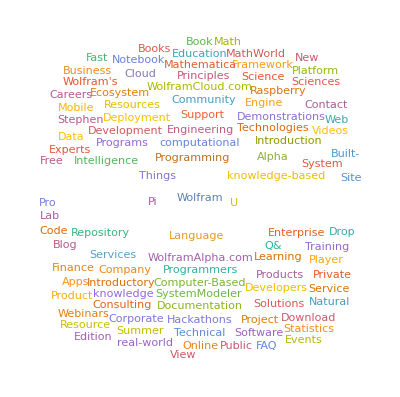

```mathematica
WordCloud[DeleteStopwords[TextWords[wolframPageText]]]
```

## Getting your Data into Shape

Useful structures for organizing data are:

Lists

Associations

Dataset

EntityStore

TimeSeries

## Data Cleaning Checklist

Check if the data:

Has consistent formatting across each row (data sample) and each column (the set of different feature values across data samples)

Has reasonable and informative feature values, free of obvious errors

Some examples of non-informative data:

A row of zeros or a column of constant feature values may not be helpful in the analysis

Unreasonable feature values (for example, negative integers for counts or implausible dates)

Feature values outside the permissible range of the data (which may require input from experts in the field)

Is free of missing data

To deal with missing data, identify:

Representation of missing data (standard notation like “NA”, “N/A”, “None”, “—”, etc. or some atypical identification/artifact of the data)

Acceptable replacements for missing data

Cost of deleting samples containing missing data

## Dealing with Missing Data

Toy dataset:

```mathematica
missingData ={{2,4,0.986,RGBColor[0.7931811599535044, 0.9794035526034883, 0.1736111262263147]},{1,5,0.0701,RGBColor[0.4966346762097671, 0.42506700252493146, 0.6020480735371379]},{2,3,0.356,RGBColor[0.17005048612802431, 0.32340985960079616, 0.5088057001465967]},{1,5,0.859,RGBColor[0.26079904402442433, 0.6645405387012917, 0.626762001873512]},{1,7,0.87,RGBColor[0.35006141637857935, 0.241784130785629, 0.8287210560502678]},{1,5,0.372,RGBColor[0.6040242604212316, 0.2495041618176539, 0.1612746936530718]},{2,"NA",0.356,RGBColor[0.5812714623512671, 0.2969407447142949, 0.49572510310649687]},{1,3,0.751,RGBColor[0.6124614477104853, 0.378535780066783, 0.878636444824388]},{1,1,0.157,RGBColor[0.664181976745267, 0.25405278277799814, 0.12343422551954197]},{1,1,"NA",RGBColor[0.5918739987770754, 0.7079781022288523, 0.7994674398394699]},{2,3,0.685,"NA"},{2,5,0.458,RGBColor[0.8929266436889802, 0.6764412122657568, 0.1876179631453354]},{2,4,0.0106,RGBColor[0.5746966560731546, 0.5532290683267522, 0.6433151858365447]},{1,0,0.697,RGBColor[0.4036028221713692, 0.6499596806079162, 0.1976339227708881]},{2,6,0.0239,RGBColor[0.2242880379356622, 0.11173047800711289, 0.0796914387814045]}};
```

```mathematica
Grid[missingData]
```

2 | 4 | 0.986 | RGBColor[0.7931811599535044, 0.9794035526034883, 0.1736111262263147]
1 | 5 | 0.0701 | RGBColor[0.4966346762097671, 0.42506700252493146, 0.6020480735371379]
2 | 3 | 0.356 | RGBColor[0.17005048612802431, 0.32340985960079616, 0.5088057001465967]
1 | 5 | 0.859 | RGBColor[0.26079904402442433, 0.6645405387012917, 0.626762001873512]
1 | 7 | 0.87 | RGBColor[0.35006141637857935, 0.241784130785629, 0.8287210560502678]
1 | 5 | 0.372 | RGBColor[0.6040242604212316, 0.2495041618176539, 0.1612746936530718]
2 | NA | 0.356 | RGBColor[0.5812714623512671, 0.2969407447142949, 0.49572510310649687]
1 | 3 | 0.751 | RGBColor[0.6124614477104853, 0.378535780066783, 0.878636444824388]
1 | 1 | 0.157 | RGBColor[0.664181976745267, 0.25405278277799814, 0.12343422551954197]
1 | 1 | NA | RGBColor[0.5918739987770754, 0.7079781022288523, 0.7994674398394699]
2 | 3 | 0.685 | NA
2 | 5 | 0.458 | RGBColor[0.8929266436889802, 0.6764412122657568, 0.1876179631453354]
2 | 4 | 0.0106 | RGBColor[0.5746966560731546, 0.5532290683267522, 0.6433151858365447]
1 | 0 | 0.697 | RGBColor[0.4036028221713692, 0.6499596806079162, 0.1976339227708881]
2 | 6 | 0.0239 | RGBColor[0.2242880379356622, 0.11173047800711289, 0.0796914387814045]

Make a copy of the dataset:

```mathematica
copyOfMissingData = missingData;
```

### Ignore Missing Values

You can ignore the samples with missing values.

Check for samples that have “NA” as a feature value: (Triple blank 0 or more - meaning NA is present anywhere)

```mathematica
Cases[copyOfMissingData,{___,"NA",___}]
```

{{2,NA,0.356,RGBColor[0.5812714623512671, 0.2969407447142949, 0.49572510310649687]},{1,1,NA,RGBColor[0.5918739987770754, 0.7079781022288523, 0.7994674398394699]},{2,3,0.685,NA}}

Delete samples with missing data:

```mathematica
cleanData =DeleteCases[copyOfMissingData,{___,"NA",___}]
```

{{2,4,0.986,RGBColor[0.7931811599535044, 0.9794035526034883, 0.1736111262263147]},{1,5,0.0701,RGBColor[0.4966346762097671, 0.42506700252493146, 0.6020480735371379]},{2,3,0.356,RGBColor[0.17005048612802431, 0.32340985960079616, 0.5088057001465967]},{1,5,0.859,RGBColor[0.26079904402442433, 0.6645405387012917, 0.626762001873512]},{1,7,0.87,RGBColor[0.35006141637857935, 0.241784130785629, 0.8287210560502678]},{1,5,0.372,RGBColor[0.6040242604212316, 0.2495041618176539, 0.1612746936530718]},{1,3,0.751,RGBColor[0.6124614477104853, 0.378535780066783, 0.878636444824388]},{1,1,0.157,RGBColor[0.664181976745267, 0.25405278277799814, 0.12343422551954197]},{2,5,0.458,RGBColor[0.8929266436889802, 0.6764412122657568, 0.1876179631453354]},{2,4,0.0106,RGBColor[0.5746966560731546, 0.5532290683267522, 0.6433151858365447]},{1,0,0.697,RGBColor[0.4036028221713692, 0.6499596806079162, 0.1976339227708881]},{2,6,0.0239,RGBColor[0.2242880379356622, 0.11173047800711289, 0.0796914387814045]}}

### Replace Missing Values

You can replace the missing value with the most common feature value.

List the feature values from the second column:

```mathematica
copyOfMissingData[[All,2]]
```

{4,5,3,5,7,5,NA,3,1,1,3,5,4,0,6}

#### Replace with most frequently occurring value

Find the most frequently occurring value in this list:

```mathematica
Commonest[copyOfMissingData[[All,2]]]
```

{5}

Replace the missing data with the most frequently occurring value:

```mathematica
copyOfMissingData[[All,2]]/."NA"-> 5
```

{4,5,3,5,7,5,5,3,1,1,3,5,4,0,6}

You can replace the missing value with the mean feature value.

#### Replace with mean

List the feature values in column three:

```mathematica
copyOfMissingData[[All,3]]
```

{0.986,0.0701,0.356,0.859,0.87,0.372,0.356,0.751,0.157,NA,0.685,0.458,0.0106,0.697,0.0239}

Select the feature values that are numbers (discarding the missing values) (makes a list with only the numeric values):

```mathematica
goodSamples = Cases[copyOfMissingData[[All,3]],_?NumericQ]
```

{0.986,0.0701,0.356,0.859,0.87,0.372,0.356,0.751,0.157,0.685,0.458,0.0106,0.697,0.0239}

Calculate the mean of the acceptable feature values:

```mathematica
goodSamplesMean = Mean[goodSamples]
```

0.475114

Replace the missing data with the mean value for this feature:

```mathematica
copyOfMissingData[[All,3]]/."NA"-> goodSamplesMean
```

{0.986,0.0701,0.356,0.859,0.87,0.372,0.356,0.751,0.157,0.475114,0.685,0.458,0.0106,0.697,0.0239}

#### Replace with mean/median/common from class

You can replace the missing value with the most common/mean/median feature value respective to class.

In this toy dataset, the feature values in column one show the class labels 1 or 2 for each data sample:

```mathematica
copyOfMissingData
```

{{2,4,0.986,RGBColor[0.7931811599535044, 0.9794035526034883, 0.1736111262263147]},{1,5,0.0701,RGBColor[0.4966346762097671, 0.42506700252493146, 0.6020480735371379]},{2,3,0.356,RGBColor[0.17005048612802431, 0.32340985960079616, 0.5088057001465967]},{1,5,0.859,RGBColor[0.26079904402442433, 0.6645405387012917, 0.626762001873512]},{1,7,0.87,RGBColor[0.35006141637857935, 0.241784130785629, 0.8287210560502678]},{1,5,0.372,RGBColor[0.6040242604212316, 0.2495041618176539, 0.1612746936530718]},{2,NA,0.356,RGBColor[0.5812714623512671, 0.2969407447142949, 0.49572510310649687]},{1,3,0.751,RGBColor[0.6124614477104853, 0.378535780066783, 0.878636444824388]},{1,1,0.157,RGBColor[0.664181976745267, 0.25405278277799814, 0.12343422551954197]},{1,1,NA,RGBColor[0.5918739987770754, 0.7079781022288523, 0.7994674398394699]},{2,3,0.685,NA},{2,5,0.458,RGBColor[0.8929266436889802, 0.6764412122657568, 0.1876179631453354]},{2,4,0.0106,RGBColor[0.5746966560731546, 0.5532290683267522, 0.6433151858365447]},{1,0,0.697,RGBColor[0.4036028221713692, 0.6499596806079162, 0.1976339227708881]},{2,6,0.0239,RGBColor[0.2242880379356622, 0.11173047800711289, 0.0796914387814045]}}

The sample with a missing value in column 3 appears to belong to class 1.

Select the samples from class 1:

```mathematica
class1SamplesCol3 =Cases[copyOfMissingData,{1,a_,b_,c_}:> b ]
```

{0.0701,0.859,0.87,0.372,0.751,0.157,NA,0.697}

Select the feature values that are numbers (discarding the missing values):

```mathematica
class1ValidSamplesCol3 =Cases[copyOfMissingData,{1,a_,b_Real,c_}:> b ]
```

{0.0701,0.859,0.87,0.372,0.751,0.157,0.697}

Calculate the mean of the acceptable feature values:

```mathematica
class1ValidSamplesCol3Mean = Mean[class1ValidSamplesCol3]
```

0.539443

Replace the missing data with the mean value for this feature, for samples belonging to class 1:

```mathematica
copyOfMissingData[[All,3]]/. "NA"-> 0.5394428571428571
```

{0.986,0.0701,0.356,0.859,0.87,0.372,0.356,0.751,0.157,0.539443,0.685,0.458,0.0106,0.697,0.0239}

#### Replace with a random value

You can replace the missing value with a random value.

Select the feature values that are numbers (discarding the missing values):

```mathematica
col3 =Cases[copyOfMissingData[[All,3]],_Real]
```

{0.986,0.0701,0.356,0.859,0.87,0.372,0.356,0.751,0.157,0.685,0.458,0.0106,0.697,0.0239}

Calculate the mean and standard deviation for these values:

```mathematica
{μ,σ}= #[col3]&/@ {Mean, StandardDeviation}
```

{0.475114,0.334849}

Draw a random sample from a normal distribution with the mean and standard deviation found previously:

```mathematica
RandomVariate[NormalDistribution[μ,σ]]
```

0.201811

Replace the missing data with the random value:

```mathematica
copyOfMissingData[[All,3]]/. "NA"->RandomVariate[NormalDistribution[μ,σ]]
```

{0.986,0.0701,0.356,0.859,0.87,0.372,0.356,0.751,0.157,0.203534,0.685,0.458,0.0106,0.697,0.0239}

Learn a distribution from the available data:

```mathematica
dist =FindDistribution[col3]
```

UniformDistribution[{-0.045991,1.06132}]

Draw a random value from the learned distribution:

```mathematica
RandomVariate[dist]
```

0.0247108

#### Hot deck imputation

You can replace the missing values with “Hot Deck Imputation”.

Revisit the dataset:

```mathematica
copyOfMissingData
```

{{2,4,0.986,RGBColor[0.7931811599535044, 0.9794035526034883, 0.1736111262263147]},{1,5,0.0701,RGBColor[0.4966346762097671, 0.42506700252493146, 0.6020480735371379]},{2,3,0.356,RGBColor[0.17005048612802431, 0.32340985960079616, 0.5088057001465967]},{1,5,0.859,RGBColor[0.26079904402442433, 0.6645405387012917, 0.626762001873512]},{1,7,0.87,RGBColor[0.35006141637857935, 0.241784130785629, 0.8287210560502678]},{1,5,0.372,RGBColor[0.6040242604212316, 0.2495041618176539, 0.1612746936530718]},{2,NA,0.356,RGBColor[0.5812714623512671, 0.2969407447142949, 0.49572510310649687]},{1,3,0.751,RGBColor[0.6124614477104853, 0.378535780066783, 0.878636444824388]},{1,1,0.157,RGBColor[0.664181976745267, 0.25405278277799814, 0.12343422551954197]},{1,1,NA,RGBColor[0.5918739987770754, 0.7079781022288523, 0.7994674398394699]},{2,3,0.685,NA},{2,5,0.458,RGBColor[0.8929266436889802, 0.6764412122657568, 0.1876179631453354]},{2,4,0.0106,RGBColor[0.5746966560731546, 0.5532290683267522, 0.6433151858365447]},{1,0,0.697,RGBColor[0.4036028221713692, 0.6499596806079162, 0.1976339227708881]},{2,6,0.0239,RGBColor[0.2242880379356622, 0.11173047800711289, 0.0796914387814045]}}

List the samples with missing data in the last column:

```mathematica
missing =Cases[copyOfMissingData,{___,"NA"}]
```

{{2,3,0.685,NA}}

List the good samples (with no missing data):

```mathematica
goodSamples = DeleteCases[copyOfMissingData,{___,"NA",___}]
```

{{2,4,0.986,RGBColor[0.7931811599535044, 0.9794035526034883, 0.1736111262263147]},{1,5,0.0701,RGBColor[0.4966346762097671, 0.42506700252493146, 0.6020480735371379]},{2,3,0.356,RGBColor[0.17005048612802431, 0.32340985960079616, 0.5088057001465967]},{1,5,0.859,RGBColor[0.26079904402442433, 0.6645405387012917, 0.626762001873512]},{1,7,0.87,RGBColor[0.35006141637857935, 0.241784130785629, 0.8287210560502678]},{1,5,0.372,RGBColor[0.6040242604212316, 0.2495041618176539, 0.1612746936530718]},{1,3,0.751,RGBColor[0.6124614477104853, 0.378535780066783, 0.878636444824388]},{1,1,0.157,RGBColor[0.664181976745267, 0.25405278277799814, 0.12343422551954197]},{2,5,0.458,RGBColor[0.8929266436889802, 0.6764412122657568, 0.1876179631453354]},{2,4,0.0106,RGBColor[0.5746966560731546, 0.5532290683267522, 0.6433151858365447]},{1,0,0.697,RGBColor[0.4036028221713692, 0.6499596806079162, 0.1976339227708881]},{2,6,0.0239,RGBColor[0.2242880379356622, 0.11173047800711289, 0.0796914387814045]}}

Find the sample that is nearest to the sample “missing,” based on feature values in columns 1, 2 and 3:

```mathematica
Nearest[goodSamples[[All,{1,2,3}]],First[missing][[{1,2,3}]]]
```

{{2,3,0.356}}

Set up Nearest to return the color (data from column 4) for the sample that is nearest to “missing” for values in columns 1, 2 and 3:

```mathematica
samples =#[[{1,2,3}]]->#[[4]]&/@goodSamples
```

{{2,4,0.986}→RGBColor[0.7931811599535044, 0.9794035526034883, 0.1736111262263147],{1,5,0.0701}→RGBColor[0.4966346762097671, 0.42506700252493146, 0.6020480735371379],{2,3,0.356}→RGBColor[0.17005048612802431, 0.32340985960079616, 0.5088057001465967],{1,5,0.859}→RGBColor[0.26079904402442433, 0.6645405387012917, 0.626762001873512],{1,7,0.87}→RGBColor[0.35006141637857935, 0.241784130785629, 0.8287210560502678],{1,5,0.372}→RGBColor[0.6040242604212316, 0.2495041618176539, 0.1612746936530718],{1,3,0.751}→RGBColor[0.6124614477104853, 0.378535780066783, 0.878636444824388],{1,1,0.157}→RGBColor[0.664181976745267, 0.25405278277799814, 0.12343422551954197],{2,5,0.458}→RGBColor[0.8929266436889802, 0.6764412122657568, 0.1876179631453354],{2,4,0.0106}→RGBColor[0.5746966560731546, 0.5532290683267522, 0.6433151858365447],{1,0,0.697}→RGBColor[0.4036028221713692, 0.6499596806079162, 0.1976339227708881],{2,6,0.0239}→RGBColor[0.2242880379356622, 0.11173047800711289, 0.0796914387814045]}

```mathematica
replacement =Nearest[samples, First[missing][[{1,2,3}]]]
```

{RGBColor[0.17005048612802431, 0.32340985960079616, 0.5088057001465967]}

Replace the missing data with the feature value from the nearest sample:

```mathematica
copyOfMissingData[[All,4]] /."NA"->  RGBColor[0.17005048612802431, 0.32340985960079616, 0.5088057001465967]
```

{RGBColor[0.7931811599535044, 0.9794035526034883, 0.1736111262263147],RGBColor[0.4966346762097671, 0.42506700252493146, 0.6020480735371379],RGBColor[0.17005048612802431, 0.32340985960079616, 0.5088057001465967],RGBColor[0.26079904402442433, 0.6645405387012917, 0.626762001873512],RGBColor[0.35006141637857935, 0.241784130785629, 0.8287210560502678],RGBColor[0.6040242604212316, 0.2495041618176539, 0.1612746936530718],RGBColor[0.5812714623512671, 0.2969407447142949, 0.49572510310649687],RGBColor[0.6124614477104853, 0.378535780066783, 0.878636444824388],RGBColor[0.664181976745267, 0.25405278277799814, 0.12343422551954197],RGBColor[0.5918739987770754, 0.7079781022288523, 0.7994674398394699],RGBColor[0.17005048612802431, 0.32340985960079616, 0.5088057001465967],RGBColor[0.8929266436889802, 0.6764412122657568, 0.1876179631453354],RGBColor[0.5746966560731546, 0.5532290683267522, 0.6433151858365447],RGBColor[0.4036028221713692, 0.6499596806079162, 0.1976339227708881],RGBColor[0.2242880379356622, 0.11173047800711289, 0.0796914387814045]}

#### Use machine learning

You can replace the missing value using a regression or classification model.

Use Predict to predict the missing value in column 3, by using the “good” columns (1, 2 and 4) as input features and column 3 as the prediction target.

Set up the input for Predict:

```mathematica
regressionInput =#[[{1,2,4}]]-> #[[3]]&/@ DeleteCases[copyOfMissingData,{___,"NA",___}]
```

{{2,4,RGBColor[0.7931811599535044, 0.9794035526034883, 0.1736111262263147]}→0.986,{1,5,RGBColor[0.4966346762097671, 0.42506700252493146, 0.6020480735371379]}→0.0701,{2,3,RGBColor[0.17005048612802431, 0.32340985960079616, 0.5088057001465967]}→0.356,{1,5,RGBColor[0.26079904402442433, 0.6645405387012917, 0.626762001873512]}→0.859,{1,7,RGBColor[0.35006141637857935, 0.241784130785629, 0.8287210560502678]}→0.87,{1,5,RGBColor[0.6040242604212316, 0.2495041618176539, 0.1612746936530718]}→0.372,{1,3,RGBColor[0.6124614477104853, 0.378535780066783, 0.878636444824388]}→0.751,{1,1,RGBColor[0.664181976745267, 0.25405278277799814, 0.12343422551954197]}→0.157,{2,5,RGBColor[0.8929266436889802, 0.6764412122657568, 0.1876179631453354]}→0.458,{2,4,RGBColor[0.5746966560731546, 0.5532290683267522, 0.6433151858365447]}→0.0106,{1,0,RGBColor[0.4036028221713692, 0.6499596806079162, 0.1976339227708881]}→0.697,{2,6,RGBColor[0.2242880379356622, 0.11173047800711289, 0.0796914387814045]}→0.0239}

Build a linear regression model to predict the target value for the sample with a missing value:

```mathematica
pf =Predict[regressionInput,Method->"LinearRegression",TrainingProgressReporting->None]
```

PredictorFunction[…]

Predict the target value for column 3:

```mathematica
pf[{1,1,RGBColor[0.5918739987770754, 0.7079781022288523, 0.7994674398394699]}]
```

0.669201

#### Missing as a special value

You can treat “Missing” as a special value.

Replace the string “NA” with the Missing expression (which can be handled seamlessly by the Wolfram Language):

```mathematica
cleanData =Replace[copyOfMissingData,"NA"-> Missing[],-1]
```

{{2,4,0.986,RGBColor[0.7931811599535044, 0.9794035526034883, 0.1736111262263147]},{1,5,0.0701,RGBColor[0.4966346762097671, 0.42506700252493146, 0.6020480735371379]},{2,3,0.356,RGBColor[0.17005048612802431, 0.32340985960079616, 0.5088057001465967]},{1,5,0.859,RGBColor[0.26079904402442433, 0.6645405387012917, 0.626762001873512]},{1,7,0.87,RGBColor[0.35006141637857935, 0.241784130785629, 0.8287210560502678]},{1,5,0.372,RGBColor[0.6040242604212316, 0.2495041618176539, 0.1612746936530718]},{2,Missing[],0.356,RGBColor[0.5812714623512671, 0.2969407447142949, 0.49572510310649687]},{1,3,0.751,RGBColor[0.6124614477104853, 0.378535780066783, 0.878636444824388]},{1,1,0.157,RGBColor[0.664181976745267, 0.25405278277799814, 0.12343422551954197]},{1,1,Missing[],RGBColor[0.5918739987770754, 0.7079781022288523, 0.7994674398394699]},{2,3,0.685,Missing[]},{2,5,0.458,RGBColor[0.8929266436889802, 0.6764412122657568, 0.1876179631453354]},{2,4,0.0106,RGBColor[0.5746966560731546, 0.5532290683267522, 0.6433151858365447]},{1,0,0.697,RGBColor[0.4036028221713692, 0.6499596806079162, 0.1976339227708881]},{2,6,0.0239,RGBColor[0.2242880379356622, 0.11173047800711289, 0.0796914387814045]}}

List the values in column 4:

```mathematica
cleanData[[All,4]]
```

{RGBColor[0.7931811599535044, 0.9794035526034883, 0.1736111262263147],RGBColor[0.4966346762097671, 0.42506700252493146, 0.6020480735371379],RGBColor[0.17005048612802431, 0.32340985960079616, 0.5088057001465967],RGBColor[0.26079904402442433, 0.6645405387012917, 0.626762001873512],RGBColor[0.35006141637857935, 0.241784130785629, 0.8287210560502678],RGBColor[0.6040242604212316, 0.2495041618176539, 0.1612746936530718],RGBColor[0.5812714623512671, 0.2969407447142949, 0.49572510310649687],RGBColor[0.6124614477104853, 0.378535780066783, 0.878636444824388],RGBColor[0.664181976745267, 0.25405278277799814, 0.12343422551954197],RGBColor[0.5918739987770754, 0.7079781022288523, 0.7994674398394699],Missing[],RGBColor[0.8929266436889802, 0.6764412122657568, 0.1876179631453354],RGBColor[0.5746966560731546, 0.5532290683267522, 0.6433151858365447],RGBColor[0.4036028221713692, 0.6499596806079162, 0.1976339227708881],RGBColor[0.2242880379356622, 0.11173047800711289, 0.0796914387814045]}

Cluster the values in column 4:

```mathematica
FindClusters[cleanData[[All,4]]]
```

{{RGBColor[0.7931811599535044, 0.9794035526034883, 0.1736111262263147],Missing[],RGBColor[0.4036028221713692, 0.6499596806079162, 0.1976339227708881]},{RGBColor[0.4966346762097671, 0.42506700252493146, 0.6020480735371379],RGBColor[0.17005048612802431, 0.32340985960079616, 0.5088057001465967],RGBColor[0.5812714623512671, 0.2969407447142949, 0.49572510310649687],RGBColor[0.2242880379356622, 0.11173047800711289, 0.0796914387814045]},{RGBColor[0.26079904402442433, 0.6645405387012917, 0.626762001873512],RGBColor[0.5918739987770754, 0.7079781022288523, 0.7994674398394699],RGBColor[0.5746966560731546, 0.5532290683267522, 0.6433151858365447]},{RGBColor[0.35006141637857935, 0.241784130785629, 0.8287210560502678],RGBColor[0.6124614477104853, 0.378535780066783, 0.878636444824388]},{RGBColor[0.6040242604212316, 0.2495041618176539, 0.1612746936530718],RGBColor[0.664181976745267, 0.25405278277799814, 0.12343422551954197],RGBColor[0.8929266436889802, 0.6764412122657568, 0.1876179631453354]}}

Plot the data in feature space:

```mathematica
FeatureSpacePlot[cleanData,LabelingFunction->Callout]
```

-Graphics-

## Feature Extraction

#### Feature extraction

FeatureExtract can be used to extract features from many types of data, including numerical, textual, sounds and images, and combinations of these.

#### Nominal to numbers

Convert nominal features (that describe some qualitative aspects of an object and are usually represented as text/string) to numbers:

```mathematica
FeatureExtract[{{"Yes","A"},{"No","A"},{"No","B"},{"Maybe","B"},{"No", "C"}}]
```

{{1.92678,1.65441,0.595318,-0.62459,-1.16134,0.760571},{-0.30864,-0.776308,0.467408,-0.62459,-1.16134,0.760573},{-0.308638,-0.776306,0.467408,1.20164,0.48431,-1.22256},{-1.00086,0.674512,-1.99754,1.20163,0.484301,-1.22256},{-0.308641,-0.776308,0.467411,-1.15409,1.35406,0.923982}}

#### Boolean to numbers

Convert Boolean features (True/False or Yes/No):

```mathematica
FeatureExtract[{{1,True},{2,True},{2,False},{1,False}}]
```

{{-1.,-0.999998,-0.999999},{1.,-1.,-1.},{1.,1.,0.999999},{-1.,0.999998,1.}}

#### Image to numbers

Extract numeric features from images:

```mathematica
FeatureExtract[{-Graphics-,-Graphics-,-Graphics- ,-Graphics-,-Graphics-,-Graphics-}]
```

{{16.9775,1.43447,3.41154,-10.0882,21.6653},{8.51812,13.1914,11.741,-12.4947,-17.493},{22.9647,-10.6604,-12.6311,14.1652,-7.76729},{-15.2263,-20.7143,18.8287,3.86606,-0.117299},{-19.4959,-3.95769,-21.8003,-12.8176,-1.52362},{-13.7381,20.7065,0.450087,17.3692,5.23589}}

#### Text to numbers

Convert text to numbers:

```mathematica
FeatureExtract[{"the cat is grey","my cat is fast","this dog is scary","the big dog"}]
```

{{-1.03721,-1.22635,2.19043},{-2.79602,-0.266957,-1.63574},{0.851446,3.0376,0.304013},{2.98179,-1.54429,-0.858706}}

#### Numeric features to standardized vector

Create a toy dataset where each column of features spans a different range of values:

```mathematica
mat = Transpose[{RandomInteger[5,10],RandomReal[1,10],RandomChoice[Range[100],10]}];
mat//MatrixForm
```

(0 | 0.152242 | 25
0 | 0.681862 | 23
1 | 0.841468 | 86
2 | 0.961674 | 68
4 | 0.196442 | 61
1 | 0.762205 | 100
4 | 0.777662 | 49
1 | 0.339288 | 19
2 | 0.352769 | 25
1 | 0.715252 | 44)

Create a standardized feature vector (shifting and rescaling elements of a list to have zero mean and unit sample variance):

```mathematica
fvmat =FeatureExtract[mat,"StandardizedVector"]
```

{{-1.17954,-1.5502,-0.930533},{-1.17954,0.377774,-1.00498},{-0.442326,0.958791,1.33997},{0.294884,1.39638,0.669983},{1.7693,-1.3893,0.409434},{-0.442326,0.670248,1.86107},{1.7693,0.726515,-0.0372213},{-0.442326,-0.8693,-1.15386},{0.294884,-0.820226,-0.930533},{-0.442326,0.499326,-0.223328}}

## Dimensionality Reduction

Dimensionality reduction can be treated as a special case of feature extraction and selection, where data is projected to a different dimension than the original feature space.

When faced with too many features, projecting data to lower dimensions helps to:

Avoid the “curse of dimensionality”—poor general performance of models overfitted on training data

Allow intuitive visualization of data points in two or three dimensions for exploratory analysis

A standard rule of thumb for training data is: number of samples = 10× number of features.

DimensionReduce projects the data to a lower-dimensional approximating manifold:

```mathematica
DimensionReduce[{"the cat is grey","my cat is fast","this dog is scary","the big dog"}]
```

{{-1.03721,-1.22635},{-2.79602,-0.266957},{0.851446,3.0376},{2.98179,-1.54429}}

Perform automatic dimensionality reduction:

```mathematica
flowers = {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
reduced = DimensionReduce[flowers,2]
```

{{-19.7772,25.6661},{-4.21945,41.3735},{-19.4827,19.1779},{-35.2321,1.5771},{-45.7432,4.57804},{-17.5393,19.2883},{-11.7713,-23.8427},{-20.2746,-16.8694},{-21.5447,-24.9094},{26.5859,6.74013},{74.4563,-0.5469},{11.6288,-4.98266},{28.149,-1.06014},{50.9785,-2.39774},{5.55013,0.443553},{52.4223,-0.513103},{-26.7549,-18.0658},{-10.3037,-21.494},{-15.8792,3.64608},{-6.78219,0.647646},{5.53374,-8.45656}}

Plot the original data in two dimensions:

```mathematica
ListPlot[MapThread[Labeled[#1,#2]&,{reduced, flowers}]]
```

-Graphics-

#### Exploring feature space

FeatureSpacePlot automatically extracts features from given data, reduces to two dimensions and creates a scatter plot.

Plot the images of flowers in two dimensions, grouping similar flowers closer together:

```mathematica
FeatureSpacePlot[flowers]
```

-Graphics-

Perform the same task, plotting in three dimensions:

```mathematica
FeatureSpacePlot3D[flowers]
```

-Graphics3D-

## Stage 3: Explore

## Exploratory Data Analysis

Exploratory data analysis (EDA) can help:

Gain an intuitive understanding of the underlying nature of the dataset

Identify relationships between variables

Formulate good questions for the actual analysis (as the explorations proceed, those questions can change)

Evaluate the quality of the data (Data QA)

Tools used in EDA can be categorized as:

Graphical or non-graphical

Univariate (exploring one feature/variable at a time) or multivariate (exploring combined behavior of more than one variable)

## Visual Exploration

### Scatter Plots

Obtain information about Fisher’s Iris dataset:

```mathematica
ExampleData[{"Statistics","FisherIris"},"LongDescription"]
```

The data set consists of 50 samples from each of three species of iris flowers.  Four features were measured from each sample, they are the length and the width of sepal and petal. This data set is often used to demonstrate classification techniques and discriminant analysis.

```mathematica
ExampleData[{"Statistics","FisherIris"},"ColumnDescriptions"]
```

{Sepal length in cm.,Sepal width in cm.,Petal length in cm.,Petal width in cm.,Species of iris}

Fetch the data:

```mathematica
irisData = ExampleData[{"Statistics","FisherIris"}];
```

Select only the setosa samples:

```mathematica
setosaSamples = Cases[irisData,{___,"setosa"}];
```

Plot the sepal length versus the sepal width for setosa:

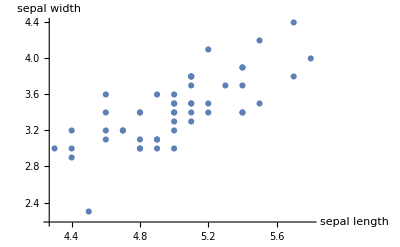

```mathematica
ListPlot[setosaSamples[[All,{1,2}]],AxesLabel->{"sepal length","sepal width"}]
```

Group the samples by class:

```mathematica
samplesByClass = GroupBy[irisData,Last];
```

Extract the class labels:

```mathematica
classLabels = Keys[samplesByClass]
```

{setosa,versicolor,virginica}

Extract the feature names:

```mathematica
features  = ExampleData[{"Statistics","FisherIris"},"ColumnDescriptions"]
```

{Sepal length in cm.,Sepal width in cm.,Petal length in cm.,Petal width in cm.,Species of iris}

A function to create a scatter plot when given the indices of the features for the Iris data:

```mathematica
scatter[i_,j_,legends_:None,labels_:None,ticks_:None]:=With[{pairsOfFeatures = samplesByClass[#][[All,{i,j}]]&/@ classLabels}, 
ListPlot[pairsOfFeatures,PlotMarkers->{{Red,6},{Green,6},{Blue,6}},Frame->True,FrameTicks->ticks,PlotLegends->legends,FrameLabel->labels]];
```

Create a scatter plot for sepal length versus sepal width for all three classes:

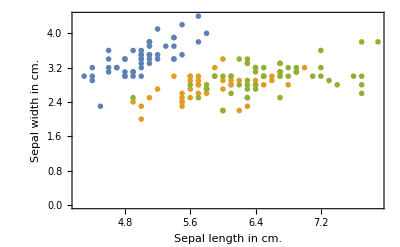

```mathematica
scatter[1,2,classLabels,features[[{1,2}]],True]
```

### Scatter Plot Matrix

A scatter plot matrix shows the pairwise relationship between multiple variables.

List the features for the Iris data:

```mathematica
features ={"Sepal length","Sepal width","Petal length","Petal width"};
```

Create multiple scatter plots to visualize how the sepal length varies with each of sepal width, petal length and petal width:

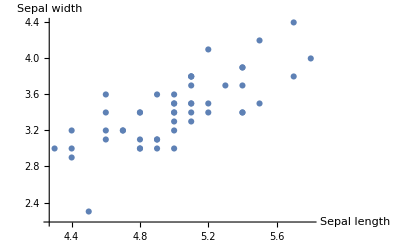
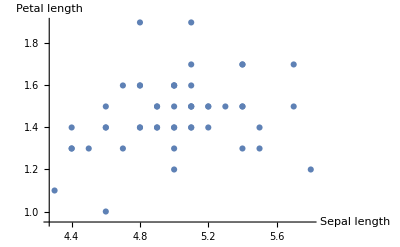
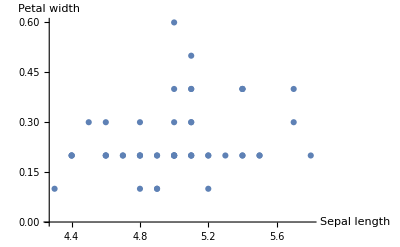

```mathematica
ListPlot[setosaSamples[[All,{1,#}]],AxesLabel->{features[[1]],features[[#]]}]& /@{2,3,4}
```

Repeat the comparison for each variable in turn to create the scatter plot matrix:

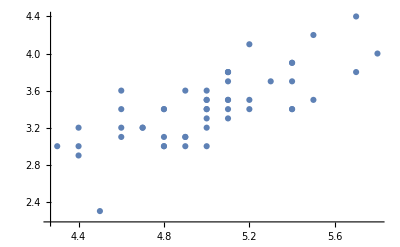
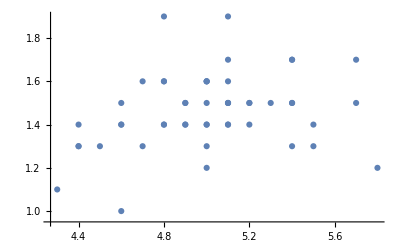
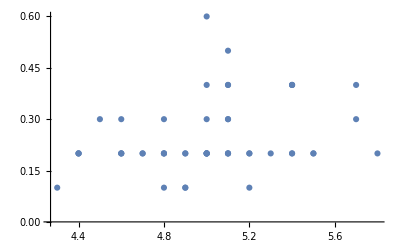
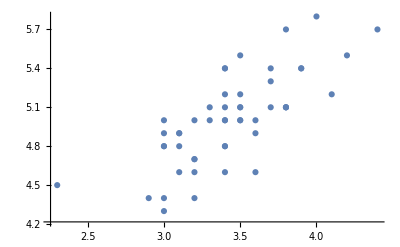
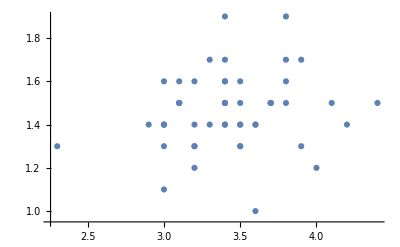
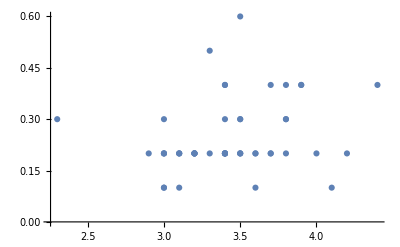
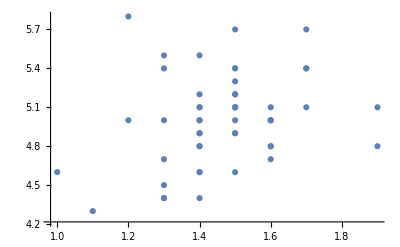
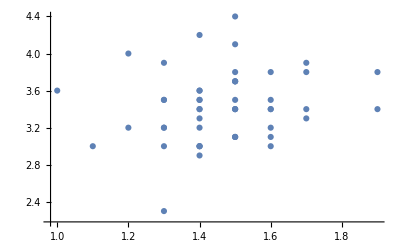
Sepal length | -Graphics- | -Graphics- | -Graphics-
-Graphics- | Sepal width | -Graphics- | -Graphics-
-Graphics- | -Graphics- | Petal length | -Graphics-
-Graphics- | -Graphics- | -Graphics- | Petal width

```mathematica
Table[If[i==j,features[[i]],ListPlot[setosaSamples[[All,{i,j}]]]],{i,4},{j,4}]//Grid
```

Create the scatter plot matrix to show the relationship between pairs of features for all three classes:

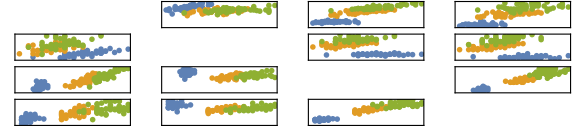

```mathematica
GraphicsGrid[Table[If[i==j,Text[Style[features[[i]],14]],scatter[i,j]],{i,4},{j,4}],ImageSize->Large]
```

## Visual Exploration

### Bar Charts and Pie Charts

Obtain information about the Old Faithful dataset:

```mathematica
ExampleData[{"Statistics","OldFaithful"},"LongDescription"]
```

Data on eruptions of Old Faithful geyser, October 1980. Variables are the duration in seconds of the current eruption, and the time in minutes to the next eruption. Collected by volunteers, and supplied by the Yellowstone National Park Geologist. Data was not collected between approximately midnight and 6 AM.

```mathematica
featureHeaders = ExampleData[{"Statistics","OldFaithful"},"ColumnDescriptions"]
```

{Eruption time in minutes,Waiting time to next eruption in minutes}

Fetch the data:

```mathematica
of=ExampleData[{"Statistics","OldFaithful"}];
```

List the eruption times:

```mathematica
of[[All,1]]
```

{3.6,1.8,3.333,2.283,4.533,2.883,4.7,3.6,1.95,4.35,1.833,3.917,4.2,1.75,4.7,2.167,1.75,4.8,1.6,4.25,1.8,1.75,3.45,3.067,4.533,3.6,1.967,4.083,3.85,4.433,4.3,4.467,3.367,4.033,3.833,2.017,1.867,4.833,1.833,4.783,4.35,1.883,4.567,1.75,4.533,3.317,3.833,2.1,4.633,2.,4.8,4.716,1.833,4.833,1.733,4.883,3.717,1.667,4.567,4.317,2.233,4.5,1.75,4.8,1.817,4.4,4.167,4.7,2.067,4.7,4.033,1.967,4.5,4.,1.983,5.067,2.017,4.567,3.883,3.6,4.133,4.333,4.1,2.633,4.067,4.933,3.95,4.517,2.167,4.,2.2,4.333,1.867,4.817,1.833,4.3,4.667,3.75,1.867,4.9,2.483,4.367,2.1,4.5,4.05,1.867,4.7,1.783,4.85,3.683,4.733,2.3,4.9,4.417,1.7,4.633,2.317,4.6,1.817,4.417,2.617,4.067,4.25,1.967,4.6,3.767,1.917,4.5,2.267,4.65,1.867,4.167,2.8,4.333,1.833,4.383,1.883,4.933,2.033,3.733,4.233,2.233,4.533,4.817,4.333,1.983,4.633,2.017,5.1,1.8,5.033,4.,2.4,4.6,3.567,4.,4.5,4.083,1.8,3.967,2.2,4.15,2.,3.833,3.5,4.583,2.367,5.,1.933,4.617,1.917,2.083,4.583,3.333,4.167,4.333,4.5,2.417,4.,4.167,1.883,4.583,4.25,3.767,2.033,4.433,4.083,1.833,4.417,2.183,4.8,1.833,4.8,4.1,3.966,4.233,3.5,4.366,2.25,4.667,2.1,4.35,4.133,1.867,4.6,1.783,4.367,3.85,1.933,4.5,2.383,4.7,1.867,3.833,3.417,4.233,2.4,4.8,2.,4.15,1.867,4.267,1.75,4.483,4.,4.117,4.083,4.267,3.917,4.55,4.083,2.417,4.183,2.217,4.45,1.883,1.85,4.283,3.95,2.333,4.15,2.35,4.933,2.9,4.583,3.833,2.083,4.367,2.133,4.35,2.2,4.45,3.567,4.5,4.15,3.817,3.917,4.45,2.,4.283,4.767,4.533,1.85,4.25,1.983,2.25,4.75,4.117,2.15,4.417,1.817,4.467}

Group them into specific bins (less than 2 minutes, more than 2 minutes but less than 3 minutes,  between 3 and 4 minutes and more than 4 minutes):

```mathematica
bc =BinCounts[of[[All,1]],{{0,2,3,4,10}}]
```

{51,46,37,138}

Visualize the information in a bar chart:

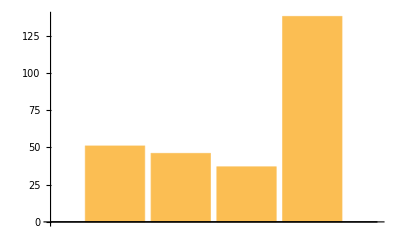

```mathematica
BarChart[BinCounts[of[[All,1]],{{0,2,3,4,10}}]]
```

Visualize the information in a pie chart:

```mathematica
PieChart[BinCounts[of[[All,1]],{{0,2,3,4,10}}]]
```

-Graphics-

Visualize the same information with appropriate labels for ease of interpretation:

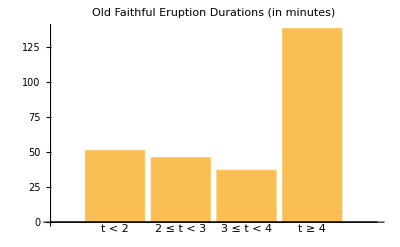

```mathematica
BarChart[bc,ChartLabels->{"t < 2","2 ≤ t < 3","3 ≤ t < 4","t ≥ 4"},PlotLabel->"Old Faithful Eruption Durations (in minutes)"]
```

```mathematica
PieChart[bc,ChartLabels->{"t < 2","2 ≤ t < 3","3 ≤ t < 4","t ≥ 4"},PlotLabel->"Old Faithful Eruption Durations (in minutes)"]
```

-Graphics-

## Visual Exploration

### Box Plots, Violin Plots and Quantile Plots

Extract the duration and wait times into separate variables:

```mathematica
{dur,wait}= Transpose[of];
```

A box-and-whisker summary of the data:

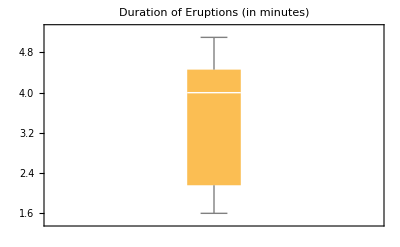

```mathematica
BoxWhiskerChart[dur,PlotLabel->"Duration of Eruptions (in minutes)"]
```

Violin plot showing probability density of the data at different values:

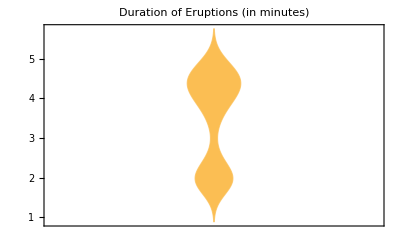

```mathematica
DistributionChart[dur,PlotLabel->"Duration of Eruptions (in minutes)"]
```

Plot empirical quantiles against quantiles of a normal distribution:

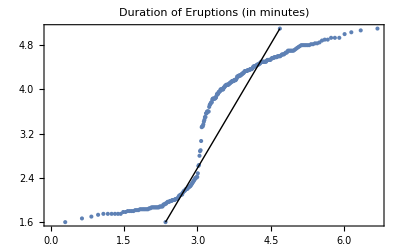

```mathematica
QuantilePlot[dur,PlotLabel->"Duration of Eruptions (in minutes)"]
```

## Visual Exploration

### Histograms

Single-variable histograms are useful for exploring one feature at a time.

Histogram of duration times of all the eruptions:

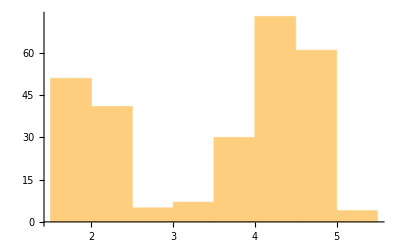

```mathematica
Histogram[dur]
```

Histogram showing the probability density function (PDF) of duration times:

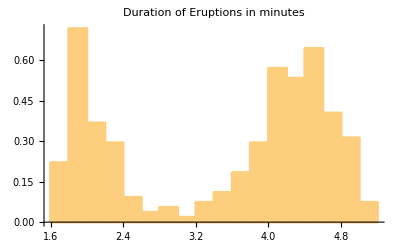

```mathematica
Histogram[dur,12,"PDF",ChartElementFunction-> "EdgeFadingRectangle",PlotLabel->"Duration of Eruptions in minutes"]
```

### Paired Histograms

Paired histograms are useful for exploring two features at the same time.

Generate random numbers from two normal distributions, with different means and standard deviations:

```mathematica
rn1 = RandomVariate[NormalDistribution[0,1],100];
rn2 = RandomVariate[NormalDistribution[1,1/2],100];
```

Create a paired histogram for the two sets of numbers:

```mathematica
PairedHistogram[rn1,rn2]
```

-Graphics-

Create a similar paired histogram for the Old Faithful data (scale the duration values to be in the same range as the waiting times):

```mathematica
scaledData=With[{dat1={Min[#],Max[#]}&[dur],dat2={Min[#],Max[#]}&[wait]},Rescale[#,dat1,dat2]&/@dur];
PairedHistogram[scaledData,wait,12,"PDF",ChartLabels-> {Style["Scaled Duration","Text"],Style["Waiting Time","Text"]}]
```

-Graphics-

### Overlaying Graphics

Data from a normal distribution with mean 0 and standard deviation 1:

```mathematica
dataDist = RandomVariate[NormalDistribution[0,1],100];
```

Compare the histogram of the data values to the original distribution:

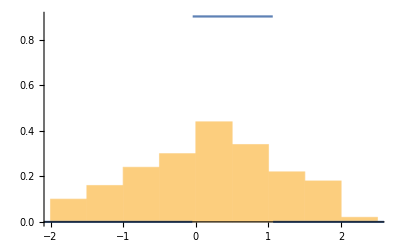

```mathematica
Show[Histogram[dataDist,10,PDF],Plot[PDF[dist,x],{x,-4,4}]]
```

Estimate a mixture distribution of two normal distributions for the duration of Old Faithful eruptions:

```mathematica
ofDist=EstimatedDistribution[wait,MixtureDistribution[{2/3,1/3},{NormalDistribution[m1,s1],NormalDistribution[m2,s2]}]]
```

MixtureDistribution[{2/3,1/3},{NormalDistribution[80.012,5.94838],NormalDistribution[54.4961,5.77335]}]

Overlay a plot of the estimated distribution on the histogram of the data values:

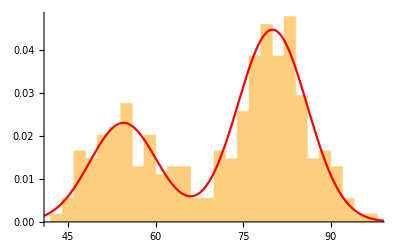

```mathematica
Show[{Histogram[wait,25,"PDF"],Plot[PDF[ofDist,x],{x,34,100},PlotStyle-> Red]}]
```

### Correlation Plots

Scatter plot of duration versus wait times:

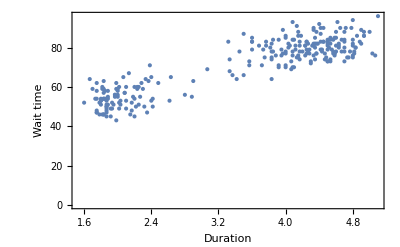

```mathematica
ListPlot[of,Frame->True,FrameLabel->{"Duration","Wait time"}]
```

Other options to visualize the multivariate data in 3D through density projections and histograms based on binning or kernel density estimation:

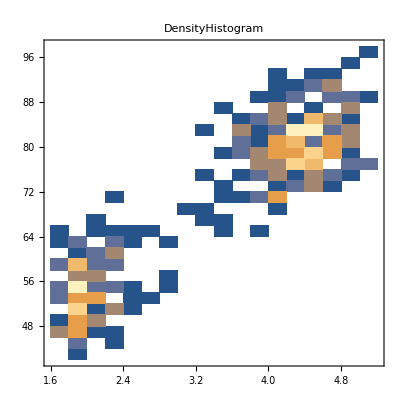

```mathematica
GraphicsGrid[{
{DensityHistogram[of,20,"PDF",PlotLabel->"DensityHistogram"],Histogram3D[of,20,"PDF",PlotLabel->"Histogram3D"],SmoothHistogram3D[of,PlotLabel->"SmoothHistogram3D"]}
},ImageSize->600]
```

## Visual Exploration

### Clustering

Find clusters in the Old Faithful data and plot the clusters in 2D:

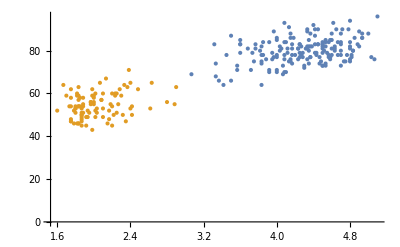

```mathematica
ListPlot[FindClusters[of,2]]
```

Create an interface to explore different numbers of clusters in the Old Faithful data, to identify interesting outliers:

```mathematica
Manipulate[ListPlot[FindClusters[of,n],PlotMarkers->Automatic],{{n,2},1,5,1},ControlType->Setter,Initialization:>(of =ExampleData[{"Statistics","OldFaithful"}])]
```

Create a toy dataset of random colors:

```mathematica
colors = RandomColor[30]
```

{RGBColor[0.542064724140944, 0.8836650465327247, 0.6440930350694636],RGBColor[0.038905981879804985, 0.37890544694781747, 0.07980502978799864],RGBColor[0.4604262963182577, 0.5944135467409581, 0.0025116816343890846],RGBColor[0.8914829657076018, 0.019589358860894857, 0.3943275212149895],RGBColor[0.5806498390653814, 0.6464559183720111, 0.5135473002778861],RGBColor[0.09103279252264196, 0.6601954933434526, 0.33884018770912716],RGBColor[0.2631996234029168, 0.9549089943245774, 0.7421172674979022],RGBColor[0.5490280782763723, 0.004840029090111164, 0.2953849653407776],RGBColor[0.14061567535036645, 0.47494744641024456, 0.2637655592553534],RGBColor[0.8013832346421261, 0.8777944205078128, 0.4656351755027932],RGBColor[0.4532174939249036, 0.873749345561974, 0.447483709112229],RGBColor[0.43607901520785886, 0.4033180557185354, 0.7537067778541322],RGBColor[0.658183914656798, 0.35270359391409234, 0.9615397686931704],RGBColor[0.8954527104269387, 0.44104940968627315, 0.9038189844830977],RGBColor[0.3459660126990107, 0.9678935469904484, 0.6075491115144718],RGBColor[0.8938426885368949, 0.3823996533525522, 0.893626814297505],RGBColor[0.24428109371804685, 0.1425846213458426, 0.027089127411482394],RGBColor[0.6454041584591539, 0.5315484888081101, 0.4884793448335132],RGBColor[0.7676147704722567, 0.8983049320222667, 0.25306236797616144],RGBColor[0.006127456819846833, 0.7783093098287712, 0.2917965201028827],RGBColor[0.49977013328371966, 0.3169194487418352, 0.49900700662075326],RGBColor[0.4447129499164224, 0.8556839062240786, 0.40926313105372447],RGBColor[0.529996630626812, 0.8818712028121671, 0.3083853448181979],RGBColor[0.9301479559347396, 0.7341594652395342, 0.49793434612044307],RGBColor[0.9628464594057444, 0.9345536759971309, 0.5543582246405667],RGBColor[0.867971119490065, 0.6243811095422858, 0.9058516361304498],RGBColor[0.16232663291341032, 0.018105366598121897, 0.01982330808041577],RGBColor[0.7131535172769903, 0.37352282195218, 0.05217783166299417],RGBColor[0.8258190959660021, 0.4182025207195321, 0.35385187157586295],RGBColor[0.10574265718048359, 0.9172039854302463, 0.7647032479804958]}

Create a weighted tree from the hierarchical clustering of data elements:

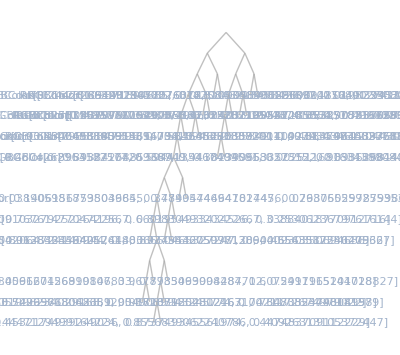

```mathematica
ClusteringTree[colors]
```

Create a dendrogram—a tree where the heights of nodes are proportional to intercluster distances:

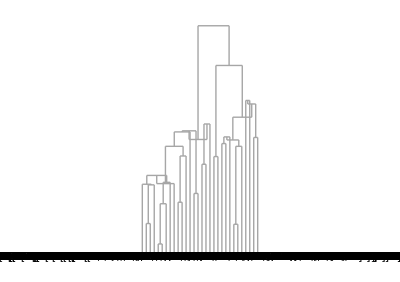

```mathematica
Dendrogram[colors, ClusterDissimilarityFunction->"Centroid"]
```

## Visual Exploration

### Visualizations in Time

Mean daily humidity of Champaign, IL, in 2018:

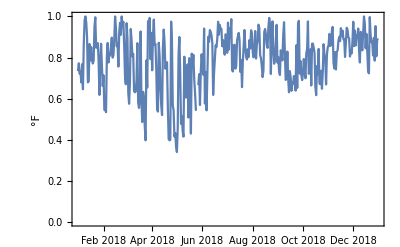

```mathematica
DateListPlot[WeatherData["KCMI", "MeanHumidity", {{2018, 1, 1}, {2018, 12, 31}, "Day"}],FrameLabel->Automatic,TargetUnits->"Fahrenheit"]
```

Mean weekly temperature of Champaign in 2018:

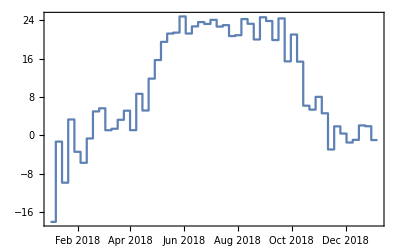

```mathematica
DateListStepPlot[WeatherData["KCMI", "MeanTemperature", {{2018, 1, 1}, {2018, 12, 31}, "Week"}]]
```

Fetch the minimum and maximum weekly temperatures of Champaign from the years 2000 and 2018:

```mathematica
minTemp =WeatherData["KCMI", "MinTemperature", {{2018, 1, 1}, {2019, 1, 1}, "Week"}];
maxTemp =WeatherData["KCMI", "MaxTemperature", {{2018, 1, 1}, {2019, 1, 1}, "Week"}];
minTemp2000 =WeatherData["KCMI", "MinTemperature", {{2000, 1, 1}, {2001,1, 1}, "Week"}];
maxTemp2000 =WeatherData["KCMI", "MaxTemperature", {{2000, 1, 1}, {2001, 1, 1}, "Week"}];
```

Create a DateListPlot of the 2018 temperatures:

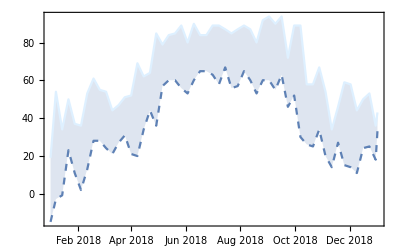

```mathematica
DateListPlot[{minTemp,maxTemp}, Joined->True,Filling->{1->{2}},TargetUnits->"Fahrenheit",PlotStyle->{Dashed,LightBlue,Blue}]
```

Shift the 2000 data and plot along with the 2018 data to compare the minimum and maximum temperatures across 18 years:

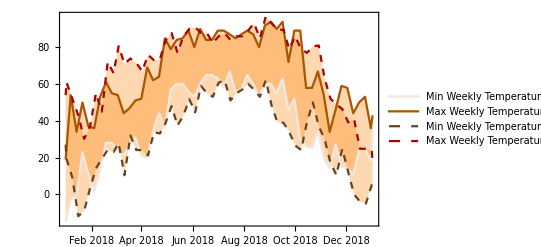

```mathematica
DateListPlot[{minTemp,maxTemp,TimeSeriesShift[minTemp2000,{18,"Year"}],TimeSeriesShift[maxTemp2000,{18,"Year"}]},]
```

## Looking at Data Differently

Different techniques can be borrowed from various fields to look at the data differently.

### Word Clouds

A word cloud can give a quick, intuitive understanding of the frequencies of certain elements in a text piece.

Import the text from the website on multiparadigm data science:

```mathematica
webpageText = Import["https://www.mpdatascience.com/"]
```

Create a word cloud showing the frequently occurring words on the page:

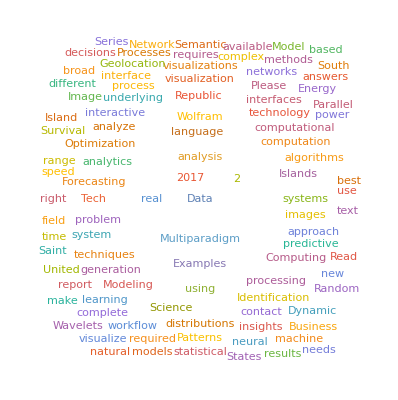

```mathematica
WordCloud[webpageText]
```

List the registered official languages in countries in the U.N.:

```mathematica
countryLanguages =EntityClass["Country","UnitedNations"][{"Name","OfficialLanguages"}]
```

Count the number of times every language occurs in this list:

```mathematica
Counts[Flatten[EntityClass["Country","UnitedNations"]["OfficialLanguages"]]]
```

<|Dari→2,Southern Pashto→1,Albanian→1,Arabic→18,Catalan→1,Portuguese→7,English→35,Spanish→12,Missing[NotAvailable]→63,German→4,Croatian→1,Bengali→1,Belarusian→1,Russian→3,Dutch→3,French→25,Dzongkha→1,Classical Quechua→2,Central Aymara→1,Standard Malay→2,Rundi→1,Khmer→1,Tetum→1,Estonian→1,Fijian→1,Finnish→1,Swedish→1,Georgian→1,Modern Greek→1,Krio→1,Indonesian→1,Persian→1,Central Kurdish→1,Irish→1,Hebrew→1,Italian→2,Swahili→2,Kirghiz→1,Lao→1,Latvian→1,Lithuanian→1,Malagasy→1,Maltese→1,Marshallese→1,Missing[None]→2,Romanian→2,Serbian→2,Nauruan→1,Western Frisian→1,Maori→1,New Zealand Sign Language→1,Bokmål Norwegian→1,Nynorsk Norwegian→1,Urdu→1,Chiripá→1,Filipino→1,Miranda do Douro→1,Kinyarwanda→1,Slovak→1,Somali→1,Sinhala→1,Swati→1,Romansch→1,Turkish→1,Ukrainian→1,Vietnamese→1|>

Create a word cloud out of the languages:

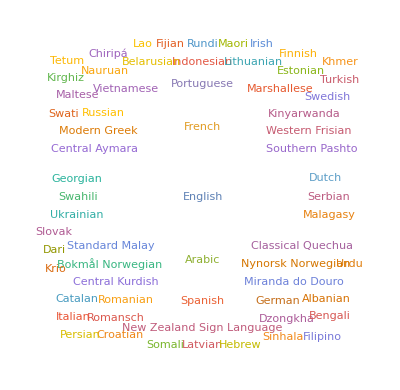

```mathematica
WordCloud[Flatten[EntityClass["Country","UnitedNations"]["OfficialLanguages"]]]
```

## Looking at Data Differently

### FeatureSpacePlot

Old Faithful Geyser eruptions data:

```mathematica
of = ExampleData[{"Statistics","OldFaithful"}];
```

Scatter plot in 2D of the two variables—eruption time and wait time to next eruption:

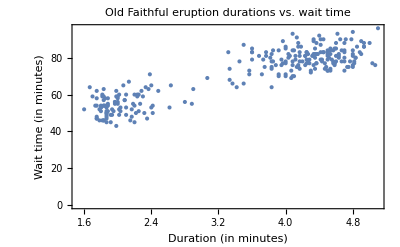

```mathematica
ListPlot[of,PlotLabel->"Old Faithful eruption durations vs. wait time",Frame->True,FrameLabel-> {"Duration (in minutes)","Wait time (in minutes)"}]
```

Fisher's Iris data:

```mathematica
irisData = ExampleData[{"Statistics","FisherIris"}];
```

Scatter plot in 2D of the two variables—sepal length and sepal width:

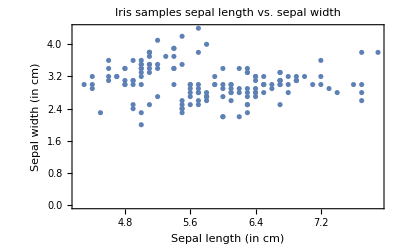

```mathematica
ListPlot[irisData[[All,{1,2}]],PlotLabel->"Iris samples sepal length vs. sepal width",Frame->True,FrameLabel-> {"Sepal length (in cm)","Sepal width (in cm)"}]
```

Intended to automate FeatureExtraction and dimensionality reduction—given any collection of objects, FeatureSpacePlot lays them out in an appropriate “feature space” for exploratory analysis.

Use FeatureSpacePlot to plot the images of three different types of objects in feature space:

```mathematica
FeatureSpacePlot[{-Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-}]
```

-Graphics-

A toy dataset of two lists of words—animals and fruits:

```mathematica
animals={"Alligator","Ant","Bear","Bee","Bird","Camel","Cat","Cheetah","Chicken","Chimpanzee","Cow","Crocodile","Deer","Dog","Dolphin","Duck","Eagle","Elephant","Fish","Fly"};
fruits={"Apple","Apricot","Avocado","Banana","Blackberry","Blueberry","Cherry","Coconut","Cranberry","Grape","Turnip","Mango","Melon","Papaya","Peach","Pineapple","Raspberry","Strawberry","Ribes","Fig"};
```

Plot the words in feature space using the pre-trained model “Glove 50-Dimensional Word Vectors Trained on Wikipedia and Gigaword 5 Data”:

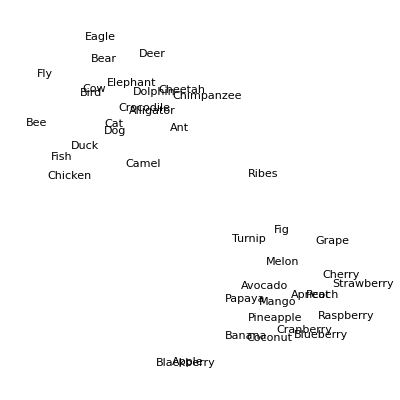

```mathematica
FeatureSpacePlot[Join[animals,fruits],FeatureExtractor->NetModel["GloVe 50-Dimensional Word Vectors Trained on Wikipedia and Gigaword 5 Data"]]
```

## Looking at Data Differently

### Geographics

Locations of earthquakes of magnitude 7 or higher around the world since 1980:

```mathematica
quakes=EarthquakeData[All,7,{{1999,1,1},{2019,9,30}},"Position"]["Values"];
```

EarthquakeData::dupdate: Earthquakes returned with duplicate dates, values may be combined.

Plot the locations of the earthquakes on a map:

```mathematica
GeoGraphics[{Red,PointSize[.01],Point[quakes]}]
```

-Graphics-

Plot the frequency of such earthquakes around the world:

```mathematica
GeoHistogram[quakes,50,PlotLegends->Automatic]
```

-Graphics-

The Ring of Fire (image courtesy: https://www.nationalgeographic.org/encyclopedia/ring-fire):

## Looking at Data Differently

### Timelines

TimelinePlot of launch dates of deep space probes:

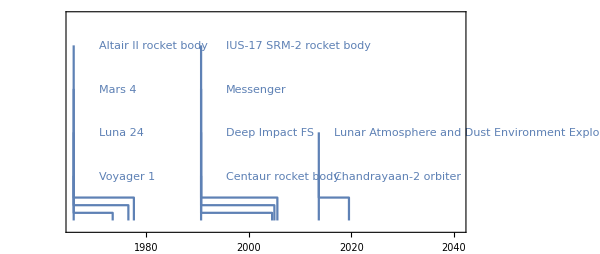

```mathematica
TimelinePlot[EntityValue[RandomEntity["DeepSpaceProbe",10],"LaunchDate","EntityAssociation"]]
```

TimelinePlot of earthquakes around Japan from March 2011:

```mathematica
earthquakes=KeySort[GroupBy[({Round[#1["Magnitude"]],#1["Period"]}&)/@Values[EarthquakeData[GeoDisk[Entity["City",{"Tokyo","Tokyo","Japan"}],Quantity[1000, "Kilometers"]],All,{{2011,3,5},{2011,3,15}}]],First->Last]];
```

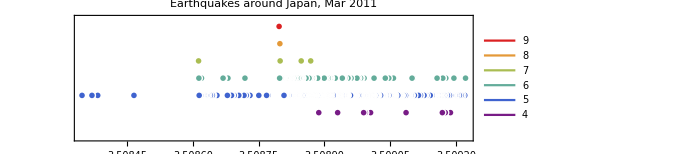

```mathematica
TimelinePlot[Values@ earthquakes,]
```

## EDA Checklist

Visualize the data in feature space

Try pairs of raw features

Project data to two or three dimensions through dimensionality reduction

Create scatter plot matrices to look at pairwise relationships across all variables

Plot distributions of all variables

Start with single distribution, single variable

Go on to joint distributions of pairs of variables

Overlay plots and graphs

Compare distribution shapes to histograms

Look for deviations

Visualize clusters of samples

Identify outliers

Look for gaps in the data

Plot time series data to identify trends

Try visualization tools from other disciplines

Generate summary statistics for each independent variable

Look at pairwise relationships between variables—correlation

## Updated by Vlad Dobrin - University of Maryland MATH299M/CMSC389W Fall 2018 August 14, 2020